```mathematica
description="Learning FeynCalc through examples.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

Successfully patched FeynArts.

```mathematica
$KeepLogDivergentScalelessIntegrals = True;
```

```mathematica
$ToolsRoot=NotebookDirectory[];
AppendTo[$Path,FileNameJoin[{$ToolsRoot,"Include"}]];
<<Tools`
<<PrettyNotation`
```

```mathematica
MakeBoxes[p1,TraditionalForm]:=SubscriptBox["p","1"];
MakeBoxes[p2,TraditionalForm]:=SubscriptBox["p","2"];
MakeBoxes[k1,TraditionalForm]:=SubscriptBox["k","1"];
MakeBoxes[k2,TraditionalForm]:=SubscriptBox["k","2"];
MakeBoxes[m1,TraditionalForm]:=SubscriptBox["m","1"];
MakeBoxes[m2,TraditionalForm]:=SubscriptBox["m","2"];
MakeBoxes[m3,TraditionalForm]:=SubscriptBox["m","3"];
MakeBoxes[x0,TraditionalForm]:=SubscriptBox["x","0"];
MakeBoxes[x1,TraditionalForm]:=SubscriptBox["x","1"];
MakeBoxes[x2,TraditionalForm]:=SubscriptBox["x","2"];
MakeBoxes[xγ,TraditionalForm]:=SubscriptBox["x","γ"];
MakeBoxes[u1,TraditionalForm]:=SubscriptBox["u","1"];
MakeBoxes[u2,TraditionalForm]:=SubscriptBox["u","2"];
MakeBoxes[uγ,TraditionalForm]:=SubscriptBox["u","γ"];
MakeBoxes[z1,TraditionalForm]:=SubscriptBox["z","1"];
MakeBoxes[z2,TraditionalForm]:=SubscriptBox["z","2"];
MakeBoxes[zγ,TraditionalForm]:=SubscriptBox["z","γ"];
MakeBoxes[a1,TraditionalForm]:=SubscriptBox["a","1"];
MakeBoxes[a2,TraditionalForm]:=SubscriptBox["a","2"];
MakeBoxes[aγ,TraditionalForm]:=SubscriptBox["a","γ"];
MakeBoxes[β1,TraditionalForm]:=SubscriptBox["β","1"];
MakeBoxes[β2,TraditionalForm]:=SubscriptBox["β","2"];
MakeBoxes[xp,TraditionalForm]:=SuperscriptBox["x","+"];
MakeBoxes[xm,TraditionalForm]:=SuperscriptBox["x","-"];
MakeBoxes[λs,TraditionalForm]:=SubscriptBox["λ","s"];
MakeBoxes[λQ,TraditionalForm]:=SubscriptBox["λ","Q"];
MakeBoxes[c1,TraditionalForm]:=SubscriptBox["c","1"];
MakeBoxes[c2,TraditionalForm]:=SubscriptBox["c","2"];
```

## 23.02

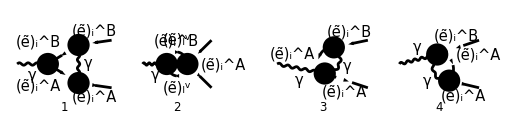

```mathematica
diagsVirt[0]=InsertFields[
CreateTopologies[1,1->2,
ExcludeTopologies->{Tadpoles,SelfEnergies}],
{V[1]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],(*Higgs*)
S[13|14],(*Squarks*)
V[2|3],(*Z, W*)
F[11|12](*Electroweakinos*)
}
];
Paint[
diagsVirt[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

### Photon bubbles

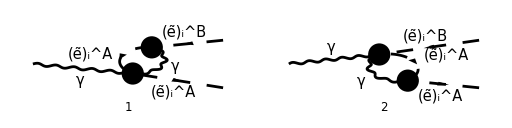

```mathematica
diagsVirt[1]=DiagramExtract[diagsVirt[0],{3,4}];
Paint[
diagsVirt[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
Mvirt[0]=FCFAConvert[
CreateFeynAmp[diagsVirt[1]],
IncomingMomenta->{p},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
ChangeDimension->D,
UndoChiralSplittings->True,
List->False,
Contract->True,
DropSumOver->True,
SMP->True
]
```

(ⅈ e^3 IndexDelta(A,B) (k·ε(p)-k_1·ε(p)))/(8 π^4 (k^2-m_l_iA^2).(k+k_1)^2)-(ⅈ e^3 IndexDelta(A,B) (k·ε(p)-k_2·ε(p)))/(8 π^4 (k^2-m_l_iA^2).(k+k_2)^2)

```mathematica
Mvirt[1]=Mvirt[0] 3/2SMP["e_Q"]//FCE//ReplaceAll[#,{
FAD[{k,MSf[A,2,i]},k+k1]->FAD[{k,MSf[B,2,i]},k+k1]
}]&
```

3/2 e_Q ((ⅈ e^3 IndexDelta(A,B) (k·ε(p)-k_1·ε(p)))/(8 π^4 (k^2-m_l_iB^2).(k+k_1)^2)-(ⅈ e^3 IndexDelta(A,B) (k·ε(p)-k_2·ε(p)))/(8 π^4 (k^2-m_l_iA^2).(k+k_2)^2))

```mathematica
Mvirt[2]=Mvirt[1]//TID[#,k,ToPaVe->True]&//FullSimplify
```

1/(32 π^2 k_1^2 k_2^2)3 e^3 e_Q IndexDelta(A,B) (k_1^2 (k_2·ε(p)) (A_0(m_l_iA^2)-(m_l_iA^2+3 k_2^2) B_0(k_2^2,0,m_l_iA^2))+k_2^2 (k_1·ε(p)) ((m_l_iB^2+3 k_1^2) B_0(k_1^2,0,m_l_iB^2)-A_0(m_l_iB^2)))

```mathematica
FCClearScalarProducts[];
SPD[p]=s;
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
SPD[k1,k2]=1/2(s-MSf[A,2,i]^2-MSf[B,2,i]^2);
```

```mathematica
Mvirt[3]=Mvirt[2]//FullSimplify
```

1/(32 π^2 m_l_iA^2 m_l_iB^2)3 e^3 e_Q IndexDelta(A,B) (m_l_iB^2 (k_2·ε(p)) (A_0(m_l_iA^2)-4 m_l_iA^2 B_0(m_l_iA^2,0,m_l_iA^2))-m_l_iA^2 (k_1·ε(p)) (A_0(m_l_iB^2)-4 m_l_iB^2 B_0(m_l_iB^2,0,m_l_iB^2)))

```mathematica
Mvirt[4]=Mvirt[3]//PaXEvaluateUV
```

(9 e^3 e_Q IndexDelta(A,B) (k_1·ε(p)))/(32 π^2 ε_UV)-(9 e^3 e_Q IndexDelta(A,B) (k_2·ε(p)))/(32 π^2 ε_UV)

```mathematica
A0[m1^2]/(4m1^2)+A0[m2^2]/(4m2^2)-B0[m1^2,0,m1^2]-B0[m2^2,0,m2^2]
%//PaXEvaluateIR
```

-B_0(m_1^2,0,m_1^2)-B_0(m_2^2,0,m_2^2)+(A_0(m_1^2))/(4 m_1^2)+(A_0(m_2^2))/(4 m_2^2)

0

### Slepton bubble

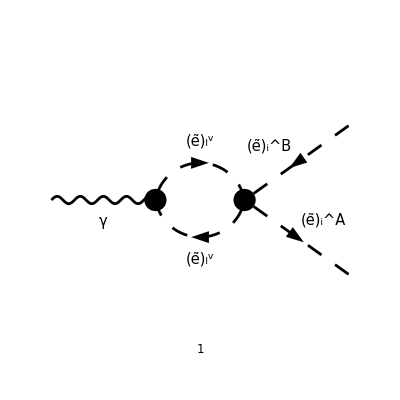

```mathematica
diagsVirt[2]=DiagramExtract[diagsVirt[0],2];
Paint[
diagsVirt[2],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
Mslepton[0]=FCFAConvert[
CreateFeynAmp[diagsVirt[2]],
IncomingMomenta->{p},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
ChangeDimension->D,
UndoChiralSplittings->True,
List->False,
Contract->True,
DropSumOver->True,
SMP->True
]
```

(ⅈ e^3 (-2 (k·ε(p))+k_1·ε(p)+k_2·ε(p)) (2 Conjugate[(USf(2,i)(B,2))] (IndexDelta(i,Gen4) Conjugate[(USf(2,i)(Sfe4,1))] ((MLE(i))^2 (cos(θ_W))^2 USf(2,i)(A,2) USf(2,i)(Sfe4,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,1) USf(2,i)(Sfe4,2))+Conjugate[(USf(2,Gen4)(Sfe4,1))] (MLE(i) (cos(θ_W))^2 MLE(Gen4) USf(2,i)(A,1) USf(2,Gen4)(Sfe4,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) USf(2,Gen4)(Sfe4,1))+2 CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) IndexDelta(i,Gen4) USf(2,i)(Sfe4,2) Conjugate[(USf(2,i)(Sfe4,2))]+2 CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) USf(2,Gen4)(Sfe4,2) Conjugate[(USf(2,Gen4)(Sfe4,2))])+Conjugate[(USf(2,i)(B,1))] (2 IndexDelta(i,Gen4) Conjugate[(USf(2,i)(Sfe4,2))] ((MLE(i))^2 (cos(θ_W))^2 USf(2,i)(A,1) USf(2,i)(Sfe4,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) USf(2,i)(Sfe4,1))+2 Conjugate[(USf(2,Gen4)(Sfe4,2))] (MLE(i) (cos(θ_W))^2 MLE(Gen4) USf(2,i)(A,2) USf(2,Gen4)(Sfe4,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,1) USf(2,Gen4)(Sfe4,2))+CB^2 m_W^2 USf(2,i)(A,1) IndexDelta(i,Gen4) USf(2,i)(Sfe4,1) Conjugate[(USf(2,i)(Sfe4,1))]+CB^2 m_W^2 USf(2,i)(A,1) USf(2,Gen4)(Sfe4,1) Conjugate[(USf(2,Gen4)(Sfe4,1))])))/(64 π^4 CB^2 m_W^2 (cos(θ_W))^2 (sin(θ_W))^2 (k^2-m_l_Gen4Sfe4^2).((k-k_1-k_2)^2-m_l_Gen4Sfe4^2))

```mathematica
Mslepton[0]//FCE//StandardForm
```

(ⅈ FAD[{k,MSf[Sfe4,2,Gen4]},{k-k1-k2,MSf[Sfe4,2,Gen4]}] SMP[e]^3 (-2 SPD[k,Polarization[p,ⅈ]]+SPD[k1,Polarization[p,ⅈ]]+SPD[k2,Polarization[p,ⅈ]]) (2 (USf[2,i][B,2])^* (2 CB^2 (USf[2,i][Sfe4,2])^* IndexDelta[i,Gen4] SMP[m_W]^2 SMP[sin_W]^2 USf[2,i][A,2] USf[2,i][Sfe4,2]+(USf[2,i][Sfe4,1])^* IndexDelta[i,Gen4] (MLE[i]^2 SMP[cos_W]^2 USf[2,i][A,2] USf[2,i][Sfe4,1]-CB^2 SMP[m_W]^2 SMP[sin_W]^2 USf[2,i][A,1] USf[2,i][Sfe4,2])+2 CB^2 (USf[2,Gen4][Sfe4,2])^* SMP[m_W]^2 SMP[sin_W]^2 USf[2,i][A,2] USf[2,Gen4][Sfe4,2]+(USf[2,Gen4][Sfe4,1])^* (-CB^2 SMP[m_W]^2 SMP[sin_W]^2 USf[2,i][A,2] USf[2,Gen4][Sfe4,1]+MLE[i] MLE[Gen4] SMP[cos_W]^2 USf[2,i][A,1] USf[2,Gen4][Sfe4,2]))+(USf[2,i][B,1])^* (CB^2 (USf[2,i][Sfe4,1])^* IndexDelta[i,Gen4] SMP[m_W]^2 USf[2,i][A,1] USf[2,i][Sfe4,1]+2 (USf[2,i][Sfe4,2])^* IndexDelta[i,Gen4] (-CB^2 SMP[m_W]^2 SMP[sin_W]^2 USf[2,i][A,2] USf[2,i][Sfe4,1]+MLE[i]^2 SMP[cos_W]^2 USf[2,i][A,1] USf[2,i][Sfe4,2])+CB^2 (USf[2,Gen4][Sfe4,1])^* SMP[m_W]^2 USf[2,i][A,1] USf[2,Gen4][Sfe4,1]+2 (USf[2,Gen4][Sfe4,2])^* (MLE[i] MLE[Gen4] SMP[cos_W]^2 USf[2,i][A,2] USf[2,Gen4][Sfe4,1]-CB^2 SMP[m_W]^2 SMP[sin_W]^2 USf[2,i][A,1] USf[2,Gen4][Sfe4,2]))))/(64 CB^2 π^4 SMP[cos_W]^2 SMP[m_W]^2 SMP[sin_W]^2)

```mathematica
Mslepton[1]=Mslepton[0]//TID[#,k,ToPaVe->True]&
```

0

```mathematica
FAD[{k,ma},{k-k1-k2,mb}]//TID[#,k,ToPaVe->True]&
```

ⅈ π^2 B_0(k_1^2+2 (k_1·k_2)+k_2^2,ma^2,mb^2)

### Radiation

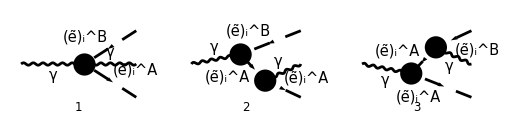

```mathematica
diagsRad[0]=InsertFields[
CreateTopologies[0,1->3,
ExcludeTopologies->{Tadpoles,SelfEnergies}],
{V[1]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],(*Higgs*)
S[13|14],(*Squarks*)
V[2|3],(*Z, W*)
F[11|12](*Electroweakinos*)
}
];
Paint[
diagsRad[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

### Full process

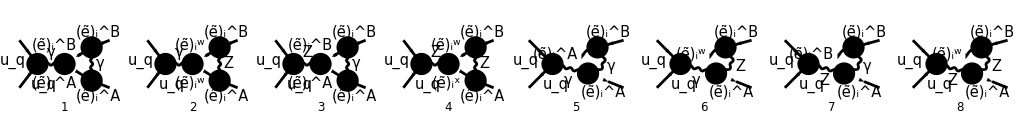

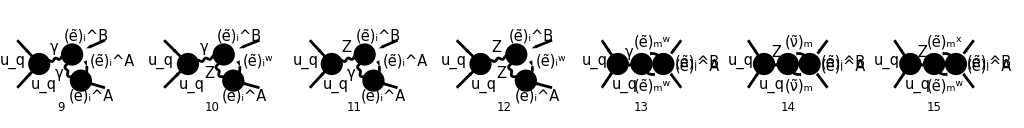

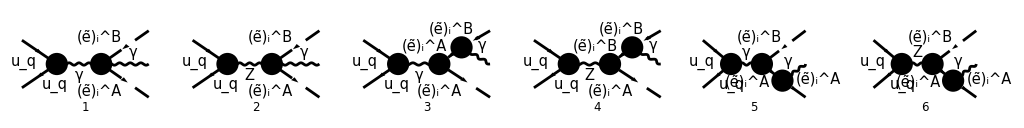

```mathematica
diagsVirt[0]=InsertFields[
CreateTopologies[1,2->2,
ExcludeTopologies->{Tadpoles,SelfEnergies}],
{F[3,{q}],-F[3,{q}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],(*Higgs*)
S[13|14],(*Squarks*)
V[3],(*Z, W*)
F[11|12](*Electroweakinos*),
F[3|4]
}
];
diagsRad[0]=InsertFields[
CreateTopologies[0,2->3,
ExcludeTopologies->{Tadpoles,SelfEnergies}],
{F[3,{q}],-F[3,{q}]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],(*Higgs*)
S[13|14],(*Squarks*)
V[3],(*Z, W*)
F[11|12](*Electroweakinos*),
F[3|4]
}
];
Paint[
diagsVirt[0],
ColumnsXRows->{8,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{1024,128}
];
Paint[
diagsRad[0],
ColumnsXRows->{8,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{1024,128}
];
```

### Derivative of B0 function

```mathematica
B0[SPD[p],0,m^2]
```

B_0(p^2,0,m^2)

```mathematica
DB0[p,0,m^2]
```

DB0(p,0,m^2)

```mathematica
DB0[p,0,m^2]
```

DB0(p,0,m^2)

```mathematica
B0[SPD[p],0,m^2]
```

B_0(p^2,0,m^2)

```mathematica
SPD[k+2p]FAD[k,{k+p,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Simplify
```

-(ⅈ (k+2 p)^2)/(π^2 k^2.((k+p)^2-m^2))

2 (m^2+p^2) B_0(p^2,0,m^2)-A_0(m^2)

2 p^2 (log(μ^2/m^2)+log(m^2/(m^2-p^2))+1/ε_UV-ℽ+2+log(4 π))+(m^2 (ε_UV log(μ^2/m^2)+(3-ℽ+log(4 π)) ε_UV+1))/ε_UV-(2 m^4 log(m^2/(m^2-p^2)))/p^2

```mathematica
1/(A B)+2/A-2/B-2(p^2-m^2-2p^2)/(A B)//ReplaceAll[#,{A->k^2,B->(k+p)^2-m^2}]&
%//FullSimplify
```

-(2 (-m^2-p^2))/(k^2 ((k+p)^2-m^2))+1/(k^2 ((k+p)^2-m^2))+2/k^2-2/((k+p)^2-m^2)

(4 p (k+p)+1)/(k^2 (k-m+p) (k+m+p))

```mathematica
Gamma[1+ϵ]
%//Series[#,{ϵ,0,2}]&
```

ϵ+1

1-ℽ ϵ+1/12 (6 ℽ^2+π^2) ϵ^2+O(ϵ^3)

```mathematica
1/((1-x)^(1+ϵ))//Series[#,{ϵ,0,1}]&
```

1/(1-x)+(ϵ log(1-x))/(x-1)+O(ϵ^2)

```mathematica
PlusDistribution[1/(1-x)^2]
```

(1/(1-x)^2)_+

## 24.02

```mathematica
Gamma[1+ϵ]
%//Series[#,{ϵ,0,1}]&
```

ϵ+1

1-ℽ ϵ+O(ϵ^2)

```mathematica
x PlusDistribution[1/(1-x)]
%//Integrate2[#,{x,0,1}]&
```

x (1/(1-x))_+

-1

```mathematica
1/(3-2ϵ)
%//Series[#,{ϵ,0,1}]&
```

1/(3-2 ϵ)

1/3+(2 ϵ)/9+O(ϵ^2)

```mathematica
1/Gamma[2-2ϵ]
%//Series[#,{ϵ,0,1}]&
```

1/(2-2 ϵ)

1+(2-2 ℽ) ϵ+O(ϵ^2)

```mathematica
Gamma[2-2ϵ]
%//Series[#,{ϵ,0,1}]&
```

2-2 ϵ

1+2 (ℽ-1) ϵ+O(ϵ^2)

```mathematica
256 Pi^3/(4 Pi^2 s λ^(3/2))
```

(64 π)/(λ^(3/2) s)

```mathematica
96Pi/λ^(3/2)2/(3s)
```

(64 π)/(λ^(3/2) s)

```mathematica
32Pi e^2/λ^(3/2) λ/(64 Pi^3)
2e^2/(4Pi^2 λ^(1/2))
```

e^2/(2 π^2 √λ)

e^2/(2 π^2 √λ)

```mathematica
A0[m^2]//PaXEvaluateUVIRSplit//FCHideEpsilon
```

m^2 Δ_UV-m^2 (-log(μ^2/(π m^2))-1+log(4 π))

```mathematica
Gamma[2-2ϵ]
%//Series[#,{ϵ,0,1}]&
```

2-2 ϵ

1+2 (ℽ-1) ϵ+O(ϵ^2)

```mathematica
1/((1+x)(1-x))-2β1/((1+x)(1-x)^2)-2β2/((1+x)^2(1-x))
%//Apart[#,x]&
```

-(2 β_1)/((1-x)^2 (x+1))-(2 β_2)/((1-x) (x+1)^2)+1/((1-x) (x+1))

-β_1/(x-1)^2+(-β_1-β_2+1)/(2 (x+1))-β_2/(x+1)^2+(β_1+β_2-1)/(2 (x-1))

```mathematica
xm-xp//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&
```

-2 √λ

```mathematica
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2a b-2a c-2b c
```

```mathematica
(xp-1)(xm-1)//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&//ReplaceAll[#,{λ->Kallen[1,β1,β2]}]&//Simplify
```

4 β_1

```mathematica
(xp+1)(xm+1)//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&//ReplaceAll[#,{λ->Kallen[1,β1,β2]}]&//Simplify
```

4 β_2

```mathematica
(xp+1)(xm-1)//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&
```

(-β_1+β_2-√λ-1) (-β_1+β_2+√λ+1)

```mathematica
(xp-1)(xm+1)//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&
```

(-β_1+β_2-√λ+1) (-β_1+β_2+√λ-1)

```mathematica
(xp+1)(xm-1)/((xp-1)(xm+1))//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&//FullSimplify
```

((β_1-β_2)^2-(√λ+1)^2)/((β_1-β_2)^2-(√λ-1)^2)

```mathematica
Kallen[1,β1,β2]
```

β_1^2-2 β_2 β_1-2 β_1+β_2^2-2 β_2+1

```mathematica
(xp-x)(x-xm)/((1+x)^2(1-x)^2)Log[(xp-x)(x-xm)]
%//Integrate[#,{x,xm,xp},Assumptions->-1<xm<xp<1]&
```

((x-x^-) (x^+-x) log((x-x^-) (x^+-x)))/((1-x)^2 (x+1)^2)

ConditionalExpression[1/4 ((x^- x^+-1) 2(x^--1)/(x^+-1)+(1-x^- x^+) 2(x^+-1)/(x^--1)-x^- x^+ 2(x^-+1)/(x^++1)+2(x^-+1)/(x^++1)+x^- x^+ 2(x^++1)/(x^-+1)-2(x^++1)/(x^-+1)+log^2(1-x^-)-log^2(x^-+1)-x^- log(1-x^-)-ⅈ π log(1-x^-)+2 log(1-x^-)-x^- log(x^-+1)+ⅈ π log(x^-+1)-2 log(x^-+1)-log^2(1-x^+)+log^2(x^++1)+x^+ log(1-x^+)+ⅈ π log(1-x^+)-2 log(1-x^+)+x^+ log(x^++1)-ⅈ π log(x^++1)+2 log(x^++1)-x^- x^+ log^2(1-x^-)+x^- x^+ log^2(x^-+1)+x^- x^+ log^2(1-x^+)-x^- x^+ log^2(x^++1)+ⅈ π x^- x^+ log(1-x^-)-x^+ log(1-x^-)-ⅈ π x^- x^+ log(x^-+1)-x^+ log(x^-+1)+x^- log(1-x^+)-ⅈ π x^- x^+ log(1-x^+)+x^- log(x^++1)+ⅈ π x^- x^+ log(x^++1)+4 x^- log(x^+-x^-)-4 x^+ log(x^+-x^-)), x^-≥0∧x^+>0]

```mathematica
(-β1/(x-1)^2-β2/(x+1)^2+(1-β1-β2)/2(1/(x+1)-1/(x-1)))(Log[xp-x]+Log[x-xm])
%//Integrate[#,{x,xm,xp},Assumptions->-1<xm<xp<1&&β1∈PositiveReals&&β2∈PositiveReals]&
```

(-β_1/(x-1)^2+1/2 (-β_1-β_2+1) (1/(x+1)-1/(x-1))-β_2/(x+1)^2) (log(x-x^-)+log(x^+-x))

ConditionalExpression[-((2 ⅈ π (x^-)^2 (x^+)^4+3 (x^-)^2 (x^+)^4-2 ⅈ π (x^+)^4-3 (x^+)^4-4 (x^-)^2 (x^+)^3+4 (x^+)^3-2 ⅈ π (x^-)^2 (x^+)^2-3 (x^-)^2 (x^+)^2+4 (x^-)^2 log(ⅇ^(1/4 x^+ (-2 ⅈ π x^+-3 x^++4))) (x^+)^2-4 log(ⅇ^(1/4 x^+ (-2 ⅈ π x^+-3 x^++4))) (x^+)^2+16 x^- β_1 log(1-x^-) (x^+)^2+16 β_1 log(1-x^-) (x^+)^2+16 x^- β_2 log(x^-+1) (x^+)^2-16 β_2 log(x^-+1) (x^+)^2-16 x^- β_1 log(1-x^+) (x^+)^2-16 β_1 log(1-x^+) (x^+)^2-16 x^- β_2 log(x^++1) (x^+)^2+16 β_2 log(x^++1) (x^+)^2+32 x^- β_1 log(x^+-x^-) (x^+)^2+32 β_1 log(x^+-x^-) (x^+)^2+32 x^- β_2 log(x^+-x^-) (x^+)^2-32 β_2 log(x^+-x^-) (x^+)^2+4 (x^-)^2 log(1-x^-) log(x^+-x^-) (x^+)^2-4 log(1-x^-) log(x^+-x^-) (x^+)^2-4 (x^-)^2 log(x^-+1) log(x^+-x^-) (x^+)^2-8 (x^-)^2 β_1 log(x^-+1) log(x^+-x^-) (x^+)^2+8 β_1 log(x^-+1) log(x^+-x^-) (x^+)^2+8 (x^-)^2 β_2 log(x^-+1) log(x^+-x^-) (x^+)^2-8 β_2 log(x^-+1) log(x^+-x^-) (x^+)^2+4 log(x^-+1) log(x^+-x^-) (x^+)^2-4 (x^-)^2 log(1-x^+) log(x^+-x^-) (x^+)^2+4 log(1-x^+) log(x^+-x^-) (x^+)^2-12 (x^-)^2 log((x^--1)/(x^+-1)) log(x^+-x^-) (x^+)^2+8 (x^-)^2 β_1 log((x^--1)/(x^+-1)) log(x^+-x^-) (x^+)^2-8 β_1 log((x^--1)/(x^+-1)) log(x^+-x^-) (x^+)^2+8 (x^-)^2 β_2 log((x^--1)/(x^+-1)) log(x^+-x^-) (x^+)^2-8 β_2 log((x^--1)/(x^+-1)) log(x^+-x^-) (x^+)^2+12 log((x^--1)/(x^+-1)) log(x^+-x^-) (x^+)^2+8 (x^-)^2 log((x^+-1)/(x^--1)) log(x^+-x^-) (x^+)^2-8 (x^-)^2 β_1 log((x^+-1)/(x^--1)) log(x^+-x^-) (x^+)^2+8 β_1 log((x^+-1)/(x^--1)) log(x^+-x^-) (x^+)^2-8 (x^-)^2 β_2 log((x^+-1)/(x^--1)) log(x^+-x^-) (x^+)^2+8 β_2 log((x^+-1)/(x^--1)) log(x^+-x^-) (x^+)^2-8 log((x^+-1)/(x^--1)) log(x^+-x^-) (x^+)^2+4 (x^-)^2 log((x^-+1)/(x^++1)) log(x^+-x^-) (x^+)^2-16 (x^-)^2 β_2 log((x^-+1)/(x^++1)) log(x^+-x^-) (x^+)^2+16 β_2 log((x^-+1)/(x^++1)) log(x^+-x^-) (x^+)^2-4 log((x^-+1)/(x^++1)) log(x^+-x^-) (x^+)^2+4 (x^-)^2 log(x^++1) log(x^+-x^-) (x^+)^2+8 (x^-)^2 β_1 log(x^++1) log(x^+-x^-) (x^+)^2-8 β_1 log(x^++1) log(x^+-x^-) (x^+)^2-8 (x^-)^2 β_2 log(x^++1) log(x^+-x^-) (x^+)^2+8 β_2 log(x^++1) log(x^+-x^-) (x^+)^2-4 log(x^++1) log(x^+-x^-) (x^+)^2-16 (x^-)^2 log((x^++1)/(x^-+1)) log(x^+-x^-) (x^+)^2+8 (x^-)^2 β_1 log((x^++1)/(x^-+1)) log(x^+-x^-) (x^+)^2-8 β_1 log((x^++1)/(x^-+1)) log(x^+-x^-) (x^+)^2+8 (x^-)^2 β_2 log((x^++1)/(x^-+1)) log(x^+-x^-) (x^+)^2-8 β_2 log((x^++1)/(x^-+1)) log(x^+-x^-) (x^+)^2+16 log((x^++1)/(x^-+1)) log(x^+-x^-) (x^+)^2-8 (x^-)^2 2(x^+-x^-)/(x^+-1) (x^+)^2+8 (x^-)^2 β_1 2(x^+-x^-)/(x^+-1) (x^+)^2-8 β_1 2(x^+-x^-)/(x^+-1) (x^+)^2+8 (x^-)^2 β_2 2(x^+-x^-)/(x^+-1) (x^+)^2-8 β_2 2(x^+-x^-)/(x^+-1) (x^+)^2+8 2(x^+-x^-)/(x^+-1) (x^+)^2+8 (x^-)^2 2(x^+-x^-)/(x^++1) (x^+)^2-8 (x^-)^2 β_1 2(x^+-x^-)/(x^++1) (x^+)^2+8 β_1 2(x^+-x^-)/(x^++1) (x^+)^2-8 (x^-)^2 β_2 2(x^+-x^-)/(x^++1) (x^+)^2+8 β_2 2(x^+-x^-)/(x^++1) (x^+)^2-8 2(x^+-x^-)/(x^++1) (x^+)^2+2 ⅈ π (x^+)^2+3 (x^+)^2+4 (x^-)^2 x^++16 (x^-)^2 β_1 log(1-x^-) x^+-16 β_1 log(1-x^-) x^++16 (x^-)^2 β_2 log(x^-+1) x^+-16 β_2 log(x^-+1) x^+-16 (x^-)^2 β_1 log(1-x^+) x^++16 β_1 log(1-x^+) x^+-16 (x^-)^2 β_2 log(x^++1) x^++16 β_2 log(x^++1) x^+-32 (x^-)^2 β_1 log(x^+-x^-) x^++32 β_1 log(x^+-x^-) x^+-32 (x^-)^2 β_2 log(x^+-x^-) x^++32 β_2 log(x^+-x^-) x^+-4 x^+-4 (x^-)^2 log(ⅇ^(1/4 x^+ (-2 ⅈ π x^+-3 x^++4)))+4 log(ⅇ^(1/4 x^+ (-2 ⅈ π x^+-3 x^++4)))+16 (x^-)^2 β_1 log(1-x^-)-16 x^- β_1 log(1-x^-)-32 β_1 log(1-x^-)-16 (x^-)^2 β_2 log(x^-+1)-16 x^- β_2 log(x^-+1)+32 β_2 log(x^-+1)-16 (x^-)^2 β_1 log(1-x^+)+16 x^- β_1 log(1-x^+)+32 β_1 log(1-x^+)+16 (x^-)^2 β_2 log(x^++1)+16 x^- β_2 log(x^++1)-32 β_2 log(x^++1)-32 (x^-)^2 β_1 log(x^+-x^-)-32 x^- β_1 log(x^+-x^-)+32 (x^-)^2 β_2 log(x^+-x^-)-32 x^- β_2 log(x^+-x^-)-4 (x^-)^2 log(1-x^-) log(x^+-x^-)+4 log(1-x^-) log(x^+-x^-)+4 (x^-)^2 log(x^-+1) log(x^+-x^-)+8 (x^-)^2 β_1 log(x^-+1) log(x^+-x^-)-8 β_1 log(x^-+1) log(x^+-x^-)-8 (x^-)^2 β_2 log(x^-+1) log(x^+-x^-)+8 β_2 log(x^-+1) log(x^+-x^-)-4 log(x^-+1) log(x^+-x^-)+4 (x^-)^2 log(1-x^+) log(x^+-x^-)-4 log(1-x^+) log(x^+-x^-)+12 (x^-)^2 log((x^--1)/(x^+-1)) log(x^+-x^-)-8 (x^-)^2 β_1 log((x^--1)/(x^+-1)) log(x^+-x^-)+8 β_1 log((x^--1)/(x^+-1)) log(x^+-x^-)-8 (x^-)^2 β_2 log((x^--1)/(x^+-1)) log(x^+-x^-)+8 β_2 log((x^--1)/(x^+-1)) log(x^+-x^-)-12 log((x^--1)/(x^+-1)) log(x^+-x^-)-8 (x^-)^2 log((x^+-1)/(x^--1)) log(x^+-x^-)+8 (x^-)^2 β_1 log((x^+-1)/(x^--1)) log(x^+-x^-)-8 β_1 log((x^+-1)/(x^--1)) log(x^+-x^-)+8 (x^-)^2 β_2 log((x^+-1)/(x^--1)) log(x^+-x^-)-8 β_2 log((x^+-1)/(x^--1)) log(x^+-x^-)+8 log((x^+-1)/(x^--1)) log(x^+-x^-)-4 (x^-)^2 log((x^-+1)/(x^++1)) log(x^+-x^-)+16 (x^-)^2 β_2 log((x^-+1)/(x^++1)) log(x^+-x^-)-16 β_2 log((x^-+1)/(x^++1)) log(x^+-x^-)+4 log((x^-+1)/(x^++1)) log(x^+-x^-)-4 (x^-)^2 log(x^++1) log(x^+-x^-)-8 (x^-)^2 β_1 log(x^++1) log(x^+-x^-)+8 β_1 log(x^++1) log(x^+-x^-)+8 (x^-)^2 β_2 log(x^++1) log(x^+-x^-)-8 β_2 log(x^++1) log(x^+-x^-)+4 log(x^++1) log(x^+-x^-)+16 (x^-)^2 log((x^++1)/(x^-+1)) log(x^+-x^-)-8 (x^-)^2 β_1 log((x^++1)/(x^-+1)) log(x^+-x^-)+8 β_1 log((x^++1)/(x^-+1)) log(x^+-x^-)-8 (x^-)^2 β_2 log((x^++1)/(x^-+1)) log(x^+-x^-)+8 β_2 log((x^++1)/(x^-+1)) log(x^+-x^-)-16 log((x^++1)/(x^-+1)) log(x^+-x^-)-8 ((x^-)^2-1) ((x^+)^2-1) (β_1+β_2-1) 2(x^--x^+)/(x^--1)+8 ((x^-)^2-1) ((x^+)^2-1) (β_1+β_2-1) 2(x^--x^+)/(x^-+1)+8 (x^-)^2 2(x^+-x^-)/(x^+-1)-8 (x^-)^2 β_1 2(x^+-x^-)/(x^+-1)+8 β_1 2(x^+-x^-)/(x^+-1)-8 (x^-)^2 β_2 2(x^+-x^-)/(x^+-1)+8 β_2 2(x^+-x^-)/(x^+-1)-8 2(x^+-x^-)/(x^+-1)-8 (x^-)^2 2(x^+-x^-)/(x^++1)+8 (x^-)^2 β_1 2(x^+-x^-)/(x^++1)-8 β_1 2(x^+-x^-)/(x^++1)+8 (x^-)^2 β_2 2(x^+-x^-)/(x^++1)-8 β_2 2(x^+-x^-)/(x^++1)+8 2(x^+-x^-)/(x^++1))/(16 (x^--1) (x^-+1) (x^+-1) (x^++1))), x^-≥0∧x^+>0]

```mathematica
%//FullSimplify
```

ConditionalExpression[1/16 (8 (β_1+β_2-1) 2(x^--x^+)/(x^--1)-8 (β_1+β_2-1) 2(x^--x^+)/(x^-+1)-8 (β_1+β_2-1) 2(x^+-x^-)/(x^+-1)+8 (β_1+β_2-1) 2(x^+-x^-)/(x^++1)-4 log(ⅇ^(1/4 x^+ (4+(-3-2 ⅈ π) x^+)))+1/(((x^-)^2-1) ((x^+)^2-1))(32 β_2 log(x^++1)+16 (β_1 (x^-+1) (x^++1) (x^-+x^+-2) log(1-x^+)+β_2 (-x^+ (x^++1)+(x^+-1) (x^-)^2+((x^+)^2-1) x^-) log(x^++1))+4 log(x^+-x^-) (4 log(x^++1)+8 (x^--x^+) (β_1 (x^-+1) (x^++1)+β_2 (x^--1) (x^+-1))-(2 β_1+2 β_2-3) ((x^-)^2-1) ((x^+)^2-1) log((x^--1)/(x^+-1))+2 (β_1+β_2-1) ((x^-)^2-1) ((x^+)^2-1) log((x^+-1)/(x^--1))-4 (β_1+β_2-(β_1+β_2-1) (x^+)^2+(β_1+β_2-1) ((x^+)^2-1) (x^-)^2) log(x^++1)+((x^-)^2-1) ((x^+)^2-1) log(1-x^+))+4 (x^-+1) (x^++1) log(1-x^-) ((x^-+x^+-x^+ x^--1) log(x^+-x^-)-4 β_1 (x^-+x^+-2))+16 (x^--1) (x^+-1) log(x^-+1) ((β_1+β_2-1) (x^-+1) (x^++1) log(x^+-x^-)-β_2 (x^-+x^++2))+((x^-)^2-1) x^+ (4+(-3-2 ⅈ π) x^+) ((x^+)^2-1))), x^-≥0]

```mathematica
(xp-x)(x-xm)
%//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&//FullSimplify
```

(x-x^-) (x^+-x)

λ-(β_1-β_2+x)^2

```mathematica
1/x Log[1-x]
%//Integrate[#,{x,a,b},Assumptions->-1<a<b<1]&
```

(log(1-x))/x

2a-2b

```mathematica
PolyLog[2,x]
```

2x

```mathematica
1/((x+1)^2(x-1)^2)
%//Apart
```

1/((x-1)^2 (x+1)^2)

1/(4 (x+1))+1/(4 (x+1)^2)-1/(4 (x-1))+1/(4 (x-1)^2)

```mathematica
Log[x]/x
%//Limit[#,x->0]&
```

(log(x))/x

Indeterminate

```mathematica
-1/(x-1)^2Log[xp-x]
%//Integrate[#,x,Assumptions->-1<xm<xp<1]&
```

-(log(x^+-x))/(x-1)^2

(log(1-x))/(x^+-1)-(log(x-x^+))/(x^+-1)+(log(x^+-x))/(x-1)

```mathematica
1/((x-a)(x-b))
%//Integrate[#,x]&
```

1/((x-a) (x-b))

(log(x-a)-log(x-b))/(a-b)

```mathematica
1/((x-a)(x-b))//Apart[#,x]&
```

1/((b-a) (x-b))+1/((a-b) (x-a))

```mathematica
(1/(x-xm)+1/(x-xp))(β1/(x-1)+β2/(x+1))
%//Apart[#,x]&
%//Integrate[#,x]&
```

(1/(x-x^-)+1/(x-x^+)) (β_1/(x-1)+β_2/(x+1))

(β_1-β_2+β_1 x^-+β_2 x^-)/((x-x^-) (x^--1) (x^-+1))+(β_1-β_2+β_1 x^++β_2 x^+)/((x-x^+) (x^+-1) (x^++1))-(β_1 (x^-+x^+-2))/((x-1) (x^--1) (x^+-1))-(β_2 (x^-+x^++2))/((x+1) (x^-+1) (x^++1))

((β_1 (x^-+1)+β_2 (x^--1)) log(x-x^-))/((x^-)^2-1)+((β_1 (x^++1)+β_2 (x^+-1)) log(x-x^+))/((x^+)^2-1)-(β_1 (x^-+x^+-2) log(x-1))/((x^--1) (x^+-1))-(β_2 (x^-+x^++2) log(x+1))/((x^-+1) (x^++1))

## 25.02

```mathematica
FCClearScalarProducts[];
SPD[q1]=SPD[q2]=0;
SPD[q1,q2]=Q^2/2;
```

```mathematica
SpinorUBarD[q2].GAD[ν].GSD[k+q2].GAD[μ].GSD[k-q1].GAD[ν].SpinorVD[q]
%//DiracSimplify//FullSimplify
```

ū(q2).γ^ν.(γ·(k+q2)).γ^μ.(γ·(k-q1)).γ^ν.v(q)

((D-2) k^2+4 (k·q2)-2 Q^2) (φ(q2)).γ^μ.(φ(-q))+(D-4) (φ(q2)).(γ·k).γ^μ.(γ·q1).(φ(-q))-2 ((D-2) k^μ+2 q2^μ) (φ(q2)).(γ·k).(φ(-q))+2 (φ(q2)).(γ·q1).γ^μ.(γ·k).(φ(-q))+4 q2^μ (φ(q2)).(γ·q1).(φ(-q))

```mathematica
FAD[k,k]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

-ⅈ/(π^2 (k^2)^2)

B_0(0,0,0)

1/ε_UV-1/ε_IR

```mathematica
Gamma[2-ϵ]
%//Series[#,{ϵ,0,1}]&
```

2-ϵ

1+(ℽ-1) ϵ+O(ϵ^2)

```mathematica
(2-2ϵ)^2/(4-2ϵ)
%//Series[#,{ϵ,0,2}]&
```

(2-2 ϵ)^2/(4-2 ϵ)

1-(3 ϵ)/2+ϵ^2/4+O(ϵ^3)

## 26.02

```mathematica
C0[m1^2,m2^2,0,m1^2,0,m2^2]
%//PaXEvaluateIR
%%//PaXEvaluateUV
```

C_0(m_1^2,m_2^2,0,m_1^2,0,m_2^2)

(log(m_1^2/m_2^2))/(2 m_1^2 ε_IR-2 m_2^2 ε_IR)

0

```mathematica
(2FVD[k,μ]+FVD[p,μ])FAD[{k,m3},{k+p,m4}]
%//TID[#,k,ToPaVe->True]&
%//PaXEvaluateUVIRSplit//Collect2[#,{FVD[p,μ]}]&
```

(2 k^μ+p^μ)/((k^2-m_3^2).((k+p)^2-m4^2))

-(ⅈ π^2 (m_3^2-m4^2) p^μ B_0(p^2,m_3^2,m4^2))/p^2+(ⅈ π^2 p^μ A_0(m_3^2))/p^2-(ⅈ π^2 p^μ A_0(m4^2))/p^2

1/(2 p^4)ⅈ π^2 p^μ (-2 m_3^2 p^2 log(μ^2/m4^2)+m_3^2 p^2 log(m_3^2/m4^2)-m4^2 p^2 log(m_3^2/m4^2)+m_3^4 log(m_3^2/m4^2)-2 m_3^2 m4^2 log(m_3^2/m4^2)-2 m_3^2 √(-2 m_3^2 m4^2-2 m_3^2 p^2+m_3^4+m4^4-2 m4^2 p^2+p^4) log((√(-2 p^2 (m_3^2+m4^2)+(m_3^2-m4^2)^2+p^4)+m_3^2+m4^2-p^2)/(2 m_3 m4))+2 m4^2 √(-2 m_3^2 m4^2-2 m_3^2 p^2+m_3^4+m4^4-2 m4^2 p^2+p^4) log((√(-2 p^2 (m_3^2+m4^2)+(m_3^2-m4^2)^2+p^4)+m_3^2+m4^2-p^2)/(2 m_3 m4))+m4^4 log(m_3^2/m4^2)+2 m_3^2 p^2 log(μ^2/m_3^2)-2 m_3^2 p^2+2 m4^2 p^2)

```mathematica
4SPD[k]/d((1-x)FVD[k1,μ]-(1-y)FVD[k2,μ])+((1-2x)FVD[k1,μ]-(1-2y)FVD[k2,μ])(SPD[k]+(x^2-2x+2-x-y+x y)m1^2+(y^2-2y+2-x-y+x y)m2^2-(2-x-y+x y)SPD[p])
%//Collect2[#,{FVD[k1,μ],FVD[k2,μ]},Factoring->FullSimplify]&
%//ReplaceAll[#,{m1->0,m2->0}]&//ReplaceAll[#,{FVD[k1,μ]->1/2(FVD[p,μ]-FVD[K,μ]),FVD[k2,μ]->1/2(FVD[p,μ]+FVD[K,μ])}]&//FullSimplify//ReplaceAll[#,SPD[p]->0]&
```

(4 k^2 ((1-x) k_1^μ-(1-y) k_2^μ))/d+((1-2 x) k_1^μ-(1-2 y) k_2^μ) (k^2+m_1^2 (x^2+x y-3 x-y+2)+m_2^2 (x y-x+y^2-3 y+2)-p^2 (x y-x-y+2))

k_1^μ ((1-2 x) (k^2+(x+y-2) (m_1^2 (x-1)+m_2^2 (y-1))+p^2 (x (-y)+x+y-2))-(4 k^2 (x-1))/d)+k_2^μ ((4 k^2 (y-1))/d-(1-2 y) (k^2+(x+y-2) (m_1^2 (x-1)+m_2^2 (y-1))+p^2 (x (-y)+x+y-2)))

(k^2 K^μ (d (x+y-1)+2 (x+y-2))-(d+2) k^2 p^μ (x-y))/d

## On-shell counterterm

```mathematica
triangle[0]=1/λQ(m1^2+m2^2-Q^2)(2Q^2B0[Q^2,m1^2,m2^2]+λQ C0[m1^2,m2^2,Q^2,m1^2,0,m2^2])-1/4(A0[m1^2]/m1^2+A0[m2^2]/m2^2)+1/(2λQ)((λQ+2(m2^2-Q^2)^2-2m1^4)B0[m1^2,0,m1^2]+(λQ+2(m1^2-Q^2)^2-2m2^4)B0[m2^2,0,m2^2])
```

((m_1^2+m_2^2-Q^2) (2 Q^2 B_0(Q^2,m_1^2,m_2^2)+λ_Q C_0(m_1^2,m_2^2,Q^2,m_1^2,0,m_2^2)))/λ_Q+((2 (m_2^2-Q^2)^2-2 m_1^4+λ_Q) B_0(m_1^2,0,m_1^2)+(2 (m_1^2-Q^2)^2-2 m_2^4+λ_Q) B_0(m_2^2,0,m_2^2))/(2 λ_Q)+1/4 (-(A_0(m_1^2))/m_1^2-(A_0(m_2^2))/m_2^2)

```mathematica
bubbles=-(B0[m1^2,0,m1^2]-A0[m1^2]/(4m1^2))+A0[m2^2]/(4m2^2)-B0[m2^2,0,m2^2]
```

-B_0(m_1^2,0,m_1^2)-B_0(m_2^2,0,m_2^2)+(A_0(m_1^2))/(4 m_1^2)+(A_0(m_2^2))/(4 m_2^2)

```mathematica
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2a b-2a c-2b c
```

```mathematica
triangle[1]=triangle[0]//ReplaceAll[#,{Q->0,λQ->Kallen[0,m1^2,m2^2]}]&//FullSimplify
```

1/4 ((2 (3 m_1^2+m_2^2) B_0(m_2^2,0,m_2^2)-2 (m_1^2+3 m_2^2) B_0(m_1^2,0,m_1^2))/(m_1^2-m_2^2)+4 (m_1^2+m_2^2) C_0(m_1^2,m_2^2,0,m_1^2,0,m_2^2)-(A_0(m_1^2))/m_1^2-(A_0(m_2^2))/m_2^2)

```mathematica
triangleIR=triangle[1]//PaXEvaluateIR
triangleUV=triangle[1]//PaXEvaluateUV
triangle[2]=triangle[1]//PaXEvaluateUVIRSplit//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->(FullSimplify[#,Assumptions->{m1∈PositiveReals,m2∈PositiveReals}]&)]&
```

((m_1^2+m_2^2) log(m_1^2/m_2^2))/(2 (m_1-m_2) (m_1+m_2) ε_IR)

1/(2 ε_UV)

((m_1^2+m_2^2) log(m_1/m_2))/((m_1-m_2) (m_1+m_2) ε_IR)-(4 (m_1^2+m_2^2) log(m_1/m_2) (-log(μ^2/m_2^2)+ℽ+log(π))+(3 m_1^2+5 m_2^2) log(μ^2/m_1^2)-(5 m_1^2+3 m_2^2) log(μ^2/m_2^2)+4 (m_1^2+m_2^2) log^2(m_1/m_2)+2 (m_1-m_2) (m_1+m_2) (-3+ℽ+log(π)))/(4 (m_1-m_2) (m_1+m_2))+1/(2 ε_UV)

```mathematica
Sin[Cos[x]^2]^2/Cos[Sin[x]^2]^2
%//Integrate[#,x,Assumptions->x∈Reals]&
```

sin^2(cos^2(x)) sec^2(sin^2(x))

Integrate[sin^2(cos^2(x)) sec^2(sin^2(x)),x,Assumptions→x∈ℝ]

## 27.02

```mathematica
C0[m1^2,m2^2,s,m1^2,0,m2^2]//PaXEvaluateUV
C0[m1^2,m2^2,s,m1^2,0,m2^2]//PaXEvaluateIR
```

0

(log((√(-2 m_1^2 (m_2^2+s)+(m_2^2-s)^2+m_1^4)+m_1^2+m_2^2-s)/(2 m_1 m_2)))/(ε_IR √(-2 m_1^2 s-2 m_2^2 s+m_1^4-2 m_2^2 m_1^2+m_2^4+s^2))

### Triangle

```mathematica
triangle[0]=1/(I Pi^2)FVD[2k+k1-k2,μ]SPD[k+2k1,k-2k2]FAD[k,{k+k1,m1},{k-k2,m2}]
```

-(ⅈ (2 k+k_1-k_2)^μ ((k+2 k_1)·(k-2 k_2)))/(π^2 k^2.((k+k_1)^2-m_1^2).((k-k_2)^2-m_2^2))

```mathematica
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k1,k2]=1/2(SPD[p]-m1^2-m2^2);
SPD[p]=0;
```

```mathematica
triangle[1]=triangle[0]//TID[#,k,ToPaVe->True]&//FullSimplify
```

-((5 m_1^2+3 m_2^2) (k_1^μ+k_2^μ) B_0(0,m_1^2,m_2^2))/(m_1^2-m_2^2)+(((5 m_1^4+6 m_2^2 m_1^2+5 m_2^4) k_1^μ+(7 m_1^4+10 m_2^2 m_1^2-m_2^4) k_2^μ) B_0(m_1^2,0,m_1^2))/((m_1^2-m_2^2)^2)+(((m_1^4-10 m_2^2 m_1^2-7 m_2^4) k_1^μ-(5 m_1^4+6 m_2^2 m_1^2+5 m_2^4) k_2^μ) B_0(m_2^2,0,m_2^2))/((m_1^2-m_2^2)^2)+2 (m_1^2+m_2^2) (k_1^μ-k_2^μ) C_0(0,m_1^2,m_2^2,m_2^2,m_1^2,0)-2 (k_1^μ+k_2^μ) B_1(0,m_2^2,m_1^2)-(k_1^μ A_0(m_1^2))/m_1^2+(k_2^μ A_0(m_2^2))/m_2^2

```mathematica
triangleIR[0]=triangle[1]//PaXEvaluateIR//FullSimplify
triangleUV[0]=triangle[1]//PaXEvaluateUV//FullSimplify
```

((m_1^2+m_2^2) (k_1^μ-k_2^μ) log(m_1^2/m_2^2))/((m_1-m_2) (m_1+m_2) ε_IR)

(k_1^μ-k_2^μ)/ε_UV

```mathematica
triangle[2]=triangle[1]//PaXEvaluateUVIRSplit//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&
```

((m_1^2+m_2^2) (k_1^μ-k_2^μ) log(m_1^2/m_2^2))/((m_1-m_2) (m_1+m_2) ε_IR)+1/(2 (m_1-m_2)^2 (m_1+m_2)^2)(k_2^μ (16 (m_1^2+m_2^2) m_1^2 log(μ^2/m_1^2)-2 (3 m_1^2+m_2^2)^2 log(μ^2/m_2^2)+2 log(m_1^2/m_2^2) ((m_2^4-m_1^4) log(μ^2/m_2^2)+3 m_2^2 m_1^2+m_1^4 (5+ℽ+log(π))-m_2^4 (-1+ℽ+log(π)))+(m_1^4-m_2^4) log^2(m_1^2/m_2^2)+(m_1-m_2) (m_1+m_2) (m_1^2 (1+2 ℽ+2 log(π))+m_2^2 (13-2 ℽ-2 log(π))))-k_1^μ (8 (m_1^2+m_2^2)^2 log(μ^2/m_2^2)-2 (5 m_1^4+6 m_2^2 m_1^2+5 m_2^4) log(μ^2/m_1^2)+2 log(m_1^2/m_2^2) ((m_2^4-m_1^4) log(μ^2/m_2^2)-3 m_2^2 m_1^2+m_1^4 (-5+ℽ+log(π))-m_2^4 (1+ℽ+log(π)))+(m_1^4-m_2^4) log^2(m_1^2/m_2^2)+(m_1-m_2) (m_1+m_2) (m_1^2 (-13+2 ℽ+2 log(π))-m_2^2 (1+2 ℽ+2 log(π)))))+(k_1^μ-k_2^μ)/ε_UV

### Bubbles

```mathematica
bubble[0]=1/(I Pi^2)(-FVD[k-k1,μ]FAD[{k,m1},k+k1]+FVD[k-k2,μ]FAD[{k,m2},k+k2])
```

-(ⅈ ((k-k_2)^μ/((k^2-m_2^2).(k+k_2)^2)-(k-k_1)^μ/((k^2-m_1^2).(k+k_1)^2)))/π^2

```mathematica
bubble[1]=bubble[0]//TID[#,k,ToPaVe->True]&//FullSimplify
```

1/2 ((k_1^μ (4 m_1^2 B_0(m_1^2,0,m_1^2)-A_0(m_1^2)))/m_1^2+(k_2^μ (A_0(m_2^2)-4 m_2^2 B_0(m_2^2,0,m_2^2)))/m_2^2)

```mathematica
bubble[2]=bubble[1]//PaXEvaluateUVIRSplit//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&
```

1/2 (k_1^μ (3 log(μ^2/m_1^2)-3 ℽ+7-3 log(π))+k_2^μ (-3 log(μ^2/m_2^2)+3 ℽ-7+3 log(π)))+(3 (k_1^μ-k_2^μ))/(2 ε_UV)

### Self-energy

```mathematica
FCClearScalarProducts[];
SPD[p]=m^2;
```

```mathematica
self[0]=1/(I Pi^2)SPD[k+2p]FAD[k,{k+p,m}]
```

-(ⅈ (k+2 p)^2)/(π^2 k^2.((k+p)^2-m^2))

```mathematica
self[1]=self[0]//TID[#,k,ToPaVe->True]&
```

2 m^2 B_0(0,0,m^2)-A_0(m^2)

```mathematica
self[2]=self[1]//PaXEvaluateUVIRSplit//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&
```

m^2/ε_UV-m^2 (-log(μ^2/m^2)+ℽ-1+log(π))

### Integration for photon vacuum polarization

```mathematica
FCClearScalarProducts[];
```

```mathematica
(x(1-x)SPD[p]+(1-x)m1^2+x m2^2)Log[x(1-x)SPD[p]+(1-x)m1^2+x m2^2]
Integrate[%,{x,0,1},Assumptions->SPD[p]∈Reals&&m1∈PositiveReals&&m2∈PositiveReals]
```

(m_1^2 (1-x)+m_2^2 x+p^2 (1-x) x) log(m_1^2 (1-x)+m_2^2 x+p^2 (1-x) x)

### Tadpoles

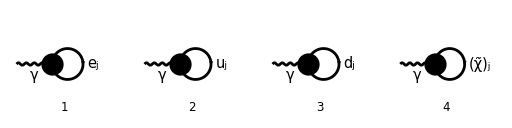

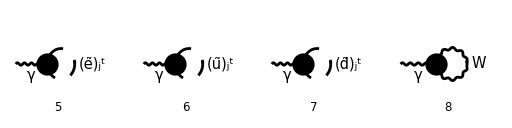

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,1->0],
{V[1]}->{},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1|2|3|4|5|6],U[1|2|3|4]}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

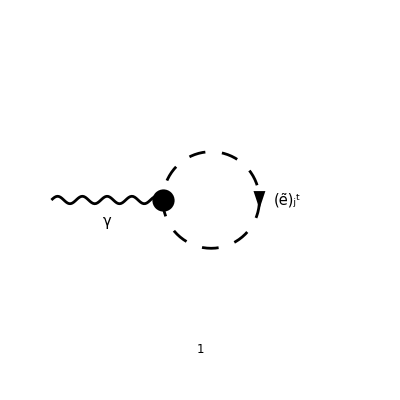

```mathematica
diags[1]=DiagramExtract[diags[0],5];
Paint[
diags[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
M[0]=FCFAConvert[
CreateFeynAmp[diags[1]],
IncomingMomenta->{p},
LoopMomenta->{k},
ChangeDimension->D,
UndoChiralSplittings->True,
List->False,
Contract->True,
DropSumOver->True,
SMP->True
]
```

-(ⅈ e (k·ε(p)))/(8 π^4 (k^2-m_l_Gen2Sfe2^2))

```mathematica
M[1]=M[0]//TID[#,k,ToPaVe->True]&
```

0

## 02.03

```mathematica
FVD[2k-p,μ]FVD[2k-p,ν]FAD[{k,m1},{k-p,m2}]
(%/(I Pi^2))//TID[#,k,ToPaVe->True]&//FCE//Collect2[#,{FVD[p,μ],FVD[p,ν],MTD[μ,ν]},Factoring->FullSimplify]&
%[[1]]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&
```

((2 k-p)^μ (2 k-p)^ν)/((k^2-m_1^2).((k-p)^2-m_2^2))

(g^μν (-(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) B_0(p^2,m_1^2,m_2^2)+(m_1^2-m_2^2+p^2) A_0(m_1^2)+(-m_1^2+m_2^2+p^2) A_0(m_2^2)))/((D-1) p^2)+(p^μ p^ν ((D (m_1^2-m_2^2)^2-2 (m_1^2+m_2^2) p^2+p^4) B_0(p^2,m_1^2,m_2^2)+A_0(m_2^2) (D (m_1-m_2) (m_1+m_2)+(D-2) p^2)+A_0(m_1^2) (D (m_2^2-m_1^2)+(D-2) p^2)))/((D-1) p^4)

(KK(1997))/(3 ε_UV)+(KK(2014))/18

```mathematica
KK[1997]//FRH
```

(3 (m_1^2+m_2^2)-p^2) g^μν

```mathematica
KK[2014]//FRH
```

1/p^4 g^μν (p^6 (-6 log((π μ^2)/m_2^2)+3 log(m_1^2/m_2^2)+6 ℽ-16-12 log(2))-3 p^4 (m_1^2 (-2 log(μ^2/m_1^2)-4 log(μ^2/m_2^2)+log(m_1^2/(4096 π^6 m_2^2))+6 ℽ-14)+m_2^2 (-6 log((π μ^2)/m_2^2)+3 log(m_1^2/m_2^2)+6 ℽ-14-12 log(2))+2 √(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) (log((√(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4)+m_1^2+m_2^2-p^2)/(m_1 m_2))-log(2)))+3 p^2 (-(m_1-m_2) (m_1+m_2) (2 m_1^2 (log(μ^2/m_2^2)-log(μ^2/m_1^2))+2 (m_1-m_2) (m_1+m_2)+(m_1^2+3 m_2^2) log(m_1^2/m_2^2))+4 m_1^2 √(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) log((√(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4)+m_1^2+m_2^2-p^2)/(2 m_1 m_2))+4 m_2^2 √(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) log((√(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4)+m_1^2+m_2^2-p^2)/(2 m_1 m_2)))+3 (m_1-m_2)^2 (m_1+m_2)^2 ((m_1-m_2) (m_1+m_2) log(m_1^2/m_2^2)-2 √(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) log((√(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4)+m_1^2+m_2^2-p^2)/(2 m_1 m_2))))

```mathematica
FVD[2k-p,μ]FVD[2k-p,ν]FAD[{k,m1},{k-p,m2}]
(%/(I Pi^2))//TID[#,k,ToPaVe->True]&//FCE//Collect2[#,{FVD[p,μ],FVD[p,ν],MTD[μ,ν]},Factoring->FullSimplify]&
%//ReplaceAll[#,{FVD[p,μ]->0}]&
%//PaXEvaluate
```

((2 k-p)^μ (2 k-p)^ν)/((k^2-m_1^2).((k-p)^2-m_2^2))

(g^μν (-(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) B_0(p^2,m_1^2,m_2^2)+(m_1^2-m_2^2+p^2) A_0(m_1^2)+(-m_1^2+m_2^2+p^2) A_0(m_2^2)))/((D-1) p^2)+(p^μ p^ν ((D (m_1^2-m_2^2)^2-2 (m_1^2+m_2^2) p^2+p^4) B_0(p^2,m_1^2,m_2^2)+A_0(m_2^2) (D (m_1-m_2) (m_1+m_2)+(D-2) p^2)+A_0(m_1^2) (D (m_2^2-m_1^2)+(D-2) p^2)))/((D-1) p^4)

(g^μν (-(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) B_0(p^2,m_1^2,m_2^2)+(m_1^2-m_2^2+p^2) A_0(m_1^2)+(-m_1^2+m_2^2+p^2) A_0(m_2^2)))/((D-1) p^2)

```mathematica
SPD[p]=0;
FVD[2k-p,μ]FVD[2k-p,ν]FAD[{k,m1},{k-p,m2}]
(%/(I Pi^2))//TID[#,k,ToPaVe->True]&//FCE//Collect2[#,{FVD[p,μ],FVD[p,ν],MTD[μ,ν]},Factoring->FullSimplify]&
%//ReplaceAll[#,{FVD[p,_]->0}]&
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

((2 k-p)^μ (2 k-p)^ν)/((k^2-m_1^2).((k-p)^2-m_2^2))

p^μ p^ν (B_0(0,m_1^2,m_2^2)+4 (B_1(0,m_1^2,m_2^2)+B_11(0,m_1^2,m_2^2)))+(2 g^μν (2 m_1^2 B_0(0,m_1^2,m_2^2)+(m_1-m_2) (m_1+m_2) B_1(0,m_1^2,m_2^2)+A_0(m_2^2)))/(D-1)

(2 g^μν (2 m_1^2 B_0(0,m_1^2,m_2^2)+(m_1-m_2) (m_1+m_2) B_1(0,m_1^2,m_2^2)+A_0(m_2^2)))/(D-1)

((m_1^2+m_2^2) g^μν)/ε_UV-(g^μν (-6 m_1^4 log(μ^2/m_2^2)+6 m_2^4 log(μ^2/m_2^2)+6 ℽ m_1^4-9 m_1^4-6 ℽ m_2^4+9 m_2^4+6 m_1^4 log(m_1^2/m_2^2)-6 m_1^4 log(π)-m_1^4 log(4096)+6 m_2^4 log(π)+m_2^4 log(4096)))/(6 (m_1-m_2) (m_1+m_2))

```mathematica
1/(-1+ϵ)//Series[#,{ϵ,0,1}]&
```

-1-ϵ+O(ϵ^2)

### Photon vacuum polarization

#### A-type

```mathematica
2I e^2 MTD[μ,ν]I FAD[{k,m}] /(2Pi)^4
%//TID[#,k,ToPaVe->True]&
Atype=%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

-(e^2 g^μν)/(8 π^4 (k^2-m^2))

-(ⅈ e^2 A_0(m^2) g^μν)/(8 π^2)

(ⅈ e^2 m^2 g^μν (-log(μ^2/m^2)+ℽ-1-log(4 π)))/(8 π^2)-(ⅈ e^2 m^2 g^μν)/(8 π^2 ε_UV)

#### B-type

```mathematica
FCClearScalarProducts[];
SPD[p]=s;
```

```mathematica
e^2/(2Pi)^4 FVD[2k-p,μ]FVD[2k-p,ν]FAD[{k,m1},{k-p,m2}]
%//TID[#,k,ToPaVe->True]&
%//FCE//ReplaceAll[#,{FVD[p,_]->0}]&
Btype=%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

(e^2 (2 k-p)^μ (2 k-p)^ν)/(16 π^4 (k^2-m_1^2).((k-p)^2-m_2^2))

-(ⅈ e^2 B_0(s,m_1^2,m_2^2) (D (m_1^2-m_2^2+s)^2 p^μ p^ν+2 (1-D) s (m_1^2-m_2^2+s) p^μ p^ν-(1-D) s^2 p^μ p^ν+4 m_1^2 s^2 g^μν-s (m_1^2-m_2^2+s)^2 g^μν-4 m_1^2 s p^μ p^ν))/(16 π^2 (1-D) s^2)-(ⅈ e^2 A_0(m_1^2) (-D (m_1^2-m_2^2+s) p^μ p^ν-2 (1-D) s p^μ p^ν+s (m_1^2-m_2^2+s) g^μν))/(16 π^2 (1-D) s^2)-(ⅈ e^2 A_0(m_2^2) (D (m_1^2-m_2^2+3 s) p^μ p^ν+2 (1-D) s p^μ p^ν-s (m_1^2-m_2^2+3 s) g^μν+4 s^2 g^μν-4 s p^μ p^ν))/(16 π^2 (1-D) s^2)

-(ⅈ e^2 B_0(s,m_1^2,m_2^2) (4 m_1^2 s^2 g^μν-s (m_1^2-m_2^2+s)^2 g^μν))/(16 π^2 (1-D) s^2)-(ⅈ e^2 A_0(m_2^2) (4 s^2 g^μν-s (m_1^2-m_2^2+3 s) g^μν))/(16 π^2 (1-D) s^2)-(ⅈ e^2 (m_1^2-m_2^2+s) A_0(m_1^2) g^μν)/(16 π^2 (1-D) s)

(ⅈ (3 m_1^2+3 m_2^2-s) g^μν e^2)/(48 ε_UV π^2)+1/(288 π^2 s^2)ⅈ (3 log(m_1^2/m_2^2) m_1^6-6 s m_1^4-9 m_2^2 log(m_1^2/m_2^2) m_1^4-3 s log(m_1^2/m_2^2) m_1^4-6 √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2)) m_1^4+6 s log(μ^2/m_1^2) m_1^4-6 s log(μ^2/m_2^2) m_1^4-18 ℽ s^2 m_1^2+42 s^2 m_1^2+12 m_2^2 s m_1^2+9 m_2^4 log(m_1^2/m_2^2) m_1^2-3 s^2 log(m_1^2/m_2^2) m_1^2-6 m_2^2 s log(m_1^2/m_2^2) m_1^2+12 m_2^2 √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2)) m_1^2+12 s √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2)) m_1^2+6 s^2 log(μ^2/m_1^2) m_1^2-6 m_2^2 s log(μ^2/m_1^2) m_1^2+12 s^2 log(μ^2/m_2^2) m_1^2+6 m_2^2 s log(μ^2/m_2^2) m_1^2+36 s^2 log(2 π) m_1^2-18 s^2 log(π) m_1^2+6 ℽ s^3-16 s^3-18 ℽ m_2^2 s^2+42 m_2^2 s^2-6 m_2^4 s-3 m_2^6 log(m_1^2/m_2^2)+3 s^3 log(m_1^2/m_2^2)-9 m_2^2 s^2 log(m_1^2/m_2^2)+9 m_2^4 s log(m_1^2/m_2^2)-6 m_2^4 √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2))-6 s^2 √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2))+12 m_2^2 s √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2))-6 s^3 log(μ^2/m_2^2)+18 m_2^2 s^2 log(μ^2/m_2^2)-12 s^3 log(2 π)+36 m_2^2 s^2 log(2 π)+6 s^3 log(π)-18 m_2^2 s^2 log(π)) g^μν e^2

```mathematica
Atype+Btype//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&
```

1/288 ⅈ KK(5676)-(ⅈ KK(5656))/(48 ε_UV)

```mathematica
KK[5656]//FRH
```

(e^2 (6 m^2-3 (m_1^2+m_2^2)+s) g^μν)/π^2

#### On-Shell

```mathematica
e^2/(2Pi)^4 FVD[2k-p,μ]FVD[2k-p,ν]FAD[{k,m},{k-p,m}]
%//TID[#,k,ToPaVe->True]&
%//FCE//ReplaceAll[#,{FVD[p,_]->0}]&
BtypeONSHELL=%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

(e^2 (2 k-p)^μ (2 k-p)^ν)/(16 π^4 (k^2-m^2).((k-p)^2-m^2))

(ⅈ e^2 g^μν (-(m^2 B_0(0,m^2,m^2))/(1-D)-(A_0(m^2))/(2 (1-D))))/(4 π^2)+(ⅈ e^2 p^μ p^ν B_0(0,m^2,m^2))/(48 π^2)

(ⅈ e^2 g^μν (-(m^2 B_0(0,m^2,m^2))/(1-D)-(A_0(m^2))/(2 (1-D))))/(4 π^2)

(ⅈ e^2 m^2 g^μν)/(8 π^2 ε_UV)-(ⅈ e^2 m^2 g^μν (-log(μ^2/m^2)+ℽ-1-log(4 π)))/(8 π^2)

```mathematica
Atype
BtypeONSHELL
```

(ⅈ e^2 m^2 g^μν (-log(μ^2/m^2)+ℽ-1-log(4 π)))/(8 π^2)-(ⅈ e^2 m^2 g^μν)/(8 π^2 ε_UV)

(ⅈ e^2 (m_1^2+m_2^2) g^μν)/(16 π^2 ε_UV)-(ⅈ e^2 g^μν (-6 m_1^4 log(μ^2/m_2^2)+6 m_2^4 log(μ^2/m_2^2)+6 ℽ m_1^4-9 m_1^4-6 ℽ m_2^4+9 m_2^4+6 m_1^4 log(m_1^2/m_2^2)-6 m_1^4 log(π)-m_1^4 log(4096)+6 m_2^4 log(π)+m_2^4 log(4096)))/(96 π^2 (m_1-m_2) (m_1+m_2))

```mathematica
Atype+BtypeONSHELL//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&
```

(ⅈ e^2 g^μν ((m_1-m_2) (m_1+m_2) (-4 m^2 log((4 π μ^2)/m^2)+4 (ℽ-1) m^2-(m_1^2+m_2^2) (-3+2 ℽ-4 log(2)))+2 (m_1^4-m_2^4) log((π μ^2)/m_2^2)-2 m_1^4 log(m_1^2/m_2^2)))/(32 π^2 (m_1-m_2) (m_1+m_2))-(ⅈ e^2 (2 m^2-m_1^2-m_2^2) g^μν)/(16 π^2 ε_UV)

```mathematica
Btype
```

(ⅈ e^2 (m_1^2+m_2^2) g^μν)/(16 π^2 ε_UV)-(ⅈ e^2 g^μν (-6 m_1^4 log(μ^2/m_2^2)+6 m_2^4 log(μ^2/m_2^2)+6 ℽ m_1^4-9 m_1^4-6 ℽ m_2^4+9 m_2^4+6 m_1^4 log(m_1^2/m_2^2)-6 m_1^4 log(π)-m_1^4 log(4096)+6 m_2^4 log(π)+m_2^4 log(4096)))/(96 π^2 (m_1-m_2) (m_1+m_2))

```mathematica
Btype-BtypeONSHELL
```

0

```mathematica
Btype//Limit[#,s->0,Assumptions->m1∈PositiveReals&&m2∈PositiveReals&&e∈PositiveReals]&
```

(ⅈ ((m_1^2-m_2^2) log(m_1^2/m_2^2)+2 Abs[m_1^2-m_2^2] log((2 m_1 m_2)/(m_1^2+m_2^2+Abs[m_1^2-m_2^2]))) g^μν) ∞

```mathematica
a Log[a]//Limit[#,a->0]&
```

0

```mathematica
A0[0]
```

0

```mathematica
A0[m^2]//PaXEvaluateUVIRSplit
%//Limit[#,m->0]&
```

m^2/ε_UV-m^2 (-log(μ^2/(π m^2))+ℽ-1)

0

## 03.03

### On-shell vertex correction

#### Triangle

```mathematica
FCClearScalarProducts[];
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k1,k2]=1/2(SPD[p]-m1^2-m2^2);
SPD[p,k1]=1/2(SPD[p]+m1^2-m2^2);
SPD[p,k2]=1/2(SPD[p]+m2^2-m1^2);
SPD[p]=0(*on-shell condition*);
```

```mathematica
triangle[0]=SMP["e"]^2/(8Pi^2)1/(I Pi^2)(FVD[k,μ]+1/2FVD[p,μ])SPD[k-k1,k+p+k2]FAD[{k,m1},k+k1,{k+p,m2}]
triangle[1]=triangle[0]//FCE//ReplaceAll[#,{FVD[p,_]->0}]&
triangle[2]=triangle[1]//TID[#,k,ToPaVe->True]&//Simplify
triangle[3]=triangle[2]//FCE//ReplaceAll[#,{
FVD[k1,μ]->1/2(FVD[p,μ]-FVD[K,μ]),
FVD[k2,μ]->1/2(FVD[p,μ]+FVD[K,μ])
}]&//ReplaceAll[#,{FVD[p,μ]->0}]&//FullSimplify
```

-(ⅈ e^2 (k^μ+p^μ/2) ((k-k_1)·(k+k_2+p)))/(8 π^4 (k^2-m_1^2).(k+k_1)^2.((k+p)^2-m_2^2))

-(ⅈ e^2 k^μ ((k-k_1)·(k+k_2+p)))/(8 π^4 (k^2-m_1^2).(k+k_1)^2.((k+p)^2-m_2^2))

-1/(16 π^2 (D-2) m_1^2 m_2^2 (m_1^2-m_2^2)^2)e^2 (m_1^2 (m_2^2 (2 (D-2) ((m_1^2-m_2^2)^2 (2 (m_1^2+m_2^2) k_1^μ C_0(0,m_1^2,m_2^2,m_2^2,m_1^2,0)+p^μ B_1(0,m_1^2,m_2^2))+B_0(m_1^2,0,m_1^2) (4 m_1^2 (m_1^2+m_2^2) p^μ-(m_1^4+2 m_2^2 m_1^2-3 m_2^4) k_1^μ)+B_0(m_2^2,0,m_2^2) ((3 m_1^4-2 m_2^2 m_1^2-m_2^4) k_1^μ-2 (m_1^2+m_2^2)^2 p^μ))-(m_1^2-m_2^2) B_0(0,m_1^2,m_2^2) (D (m_1^2-m_2^2) k_1^μ+2 ((D-3) m_1^2+(2 D-3) m_2^2) p^μ+2 (m_1^2-m_2^2) k_2^μ))+A_0(m_2^2) (-((m_1^2-m_2^2) ((D-2) m_1^2+m_2^2) k_1^μ)+((D-2) m_1^4+(D-3) m_2^4+m_2^2 m_1^2) p^μ+(m_2^4-m_1^2 m_2^2) k_2^μ))+m_2^2 A_0(m_1^2) ((m_1^2-m_2^2) ((D-2) m_2^2+m_1^2) k_1^μ+m_1^2 (((3-2 D) m_1^2+m_2^2) p^μ+(m_1^2-m_2^2) k_2^μ)))

(e^2 K^μ (m_2^2 m_1^2 ((m_2^2-m_1^2) B_0(0,m_1^2,m_2^2)-2 (m_1^2+3 m_2^2) B_0(m_1^2,0,m_1^2)+2 (3 m_1^2+m_2^2) B_0(m_2^2,0,m_2^2)+4 (m_1^4-m_2^4) C_0(0,m_1^2,m_2^2,m_2^2,m_1^2,0))+m_1^4 (-A_0(m_2^2))+m_2^4 A_0(m_1^2)))/(32 π^2 m_1^2 (m_1-m_2) m_2^2 (m_1+m_2))

```mathematica
triangle[4]=triangle[3]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FullSimplify//FCE
triangle[5]=((triangle[4]/FVD[K,μ])//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&)FVD[K,μ]
```

(e^2 K^μ (log(m_1^2/m_2^2) ε_UV (2 (m_1^2+m_2^2) ε_IR log((4 π μ^2)/m_2^2)+m_1^2 (-2 ℽ ε_IR+ε_IR+2)-2 m_2^2 (ℽ ε_IR-1))+ε_IR (-(2 m_1^2+5 m_2^2) ε_UV log(μ^2/m_1^2)+(4 m_1^2+3 m_2^2) ε_UV log(μ^2/m_2^2)-2 (m_1-m_2) (m_1+m_2) ((-3+ℽ-log(4 π)) ε_UV-1))+(m_1^2+m_2^2) (-ε_IR) log^2(m_1^2/m_2^2) ε_UV))/(32 π^2 (m_1-m_2) (m_1+m_2) ε_IR ε_UV)

K^μ ((KK(6066))/(16 ε_IR)+(KK(6067))/(16 ε_UV)-(KK(6068))/32)

#### Bubbles

```mathematica
bubbles[0]=SMP["e"]^2/(8Pi^2)1/(I Pi^2)(-(FVD[k,μ]-FVD[k1,μ])FAD[{k,m1},k+k1]+(FVD[k,μ]-FVD[k2,μ])FAD[{k,m2},k+k2])
bubbles[1]=bubbles[0]//TID[#,k,ToPaVe->True]&//Simplify
bubbles[2]=bubbles[1]//FCE//ReplaceAll[#,{
FVD[k1,μ]->1/2(FVD[p,μ]-FVD[K,μ]),
FVD[k2,μ]->1/2(FVD[p,μ]+FVD[K,μ])
}]&//ReplaceAll[#,{FVD[p,μ]->0}]&//FullSimplify
```

-(ⅈ e^2 ((k_1^μ-k^μ)/((k^2-m_1^2).(k+k_1)^2)+(k^μ-k_2^μ)/((k^2-m_2^2).(k+k_2)^2)))/(8 π^4)

(e^2 (m_1^2 (k_2^μ (A_0(m_2^2)-4 m_2^2 B_0(m_2^2,0,m_2^2))+4 m_2^2 k_1^μ B_0(m_1^2,0,m_1^2))-m_2^2 k_1^μ A_0(m_1^2)))/(16 π^2 m_1^2 m_2^2)

(e^2 K^μ (m_1^2 (A_0(m_2^2)-4 m_2^2 (B_0(m_1^2,0,m_1^2)+B_0(m_2^2,0,m_2^2)))+m_2^2 A_0(m_1^2)))/(32 π^2 m_1^2 m_2^2)

```mathematica
bubbles[3]=bubbles[2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FCE
bubbles[4]=((bubbles[3]/FVD[K,μ])//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&)FVD[K,μ]
```

(e^2 K^μ (-3 log(μ^2/m_1^2)-3 log(μ^2/m_2^2)+6 ℽ-14-6 log(4 π)))/(32 π^2)-(3 e^2 K^μ)/(16 π^2 ε_UV)

K^μ ((KK(6203))/32-(3 KK(6067))/(16 ε_UV))

#### Results

```mathematica
triangle[5]
KK[6066]//FRH
KK[6067]//FRH
KK[6068]//FRH
```

K^μ ((KK(6066))/(16 ε_IR)+(KK(6067))/(16 ε_UV)-(KK(6068))/32)

(e^2 (m_1^2+m_2^2) log(m_1^2/m_2^2))/(π^2 (m_1-m_2) (m_1+m_2))

e^2/π^2

(e^2 (log(m_1^2/m_2^2) (-2 (m_1^2+m_2^2) log((4 π μ^2)/m_2^2)+(2 ℽ-1) m_1^2+2 ℽ m_2^2)+(2 m_1^2+5 m_2^2) log(μ^2/m_1^2)-(4 m_1^2+3 m_2^2) log(μ^2/m_2^2)+(m_1^2+m_2^2) log^2(m_1^2/m_2^2)+2 (m_1-m_2) (m_1+m_2) (-3+ℽ-log(4 π))))/(π^2 (m_1-m_2) (m_1+m_2))

```mathematica
bubbles[4]
KK[6203]//FRH
KK[6067]//FRH
```

K^μ ((KK(6203))/32-(3 KK(6067))/(16 ε_UV))

(e^2 (-3 log(μ^2/m_1^2)-3 log(μ^2/m_2^2)+6 ℽ-14-6 log(4 π)))/π^2

e^2/π^2

### On-shell scheme but for massive Z-boson

```mathematica
FCClearScalarProducts[];
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k1,k2]=1/2(SPD[p]-m1^2-m2^2);
SPD[p,k1]=1/2(SPD[p]+m1^2-m2^2);
SPD[p,k2]=1/2(SPD[p]+m2^2-m1^2);
SPD[p]=SMP["m_Z"]^2(*on-shell condition*);
```

```mathematica
triangle[0]=SMP["e"]^2/(8Pi^2)1/(I Pi^2)(FVD[k,μ]+1/2FVD[p,μ])SPD[k-k1,k+p+k2]FAD[{k,m1},k+k1,{k+p,m2}]
triangle[1]=triangle[0]//FCE//ReplaceAll[#,{FVD[p,_]->0}]&
triangle[2]=triangle[1]//TID[#,k,ToPaVe->True]&//Simplify
triangle[3]=triangle[2]//FCE//ReplaceAll[#,{
FVD[k1,μ]->1/2(FVD[p,μ]-FVD[K,μ]),
FVD[k2,μ]->1/2(FVD[p,μ]+FVD[K,μ])
}]&//ReplaceAll[#,{FVD[p,μ]->0}]&//FullSimplify
```

-(ⅈ e^2 (k^μ+p^μ/2) ((k-k_1)·(k+k_2+p)))/(8 π^4 (k^2-m_1^2).(k+k_1)^2.((k+p)^2-m_2^2))

-(ⅈ e^2 k^μ ((k-k_1)·(k+k_2+p)))/(8 π^4 (k^2-m_1^2).(k+k_1)^2.((k+p)^2-m_2^2))

1/(16 π^2 m_Z^2)e^2 (1/((D-2) (m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))(2 (D-2) m_Z^2 (B_0(m_2^2,0,m_2^2) (k_1^μ (-3 m_Z^4+2 (3 m_1^2+m_2^2) m_Z^2-3 m_1^4+2 m_2^2 m_1^2+m_2^4)+2 (-m_Z^2+m_1^2+m_2^2)^2 p^μ)+B_0(m_1^2,0,m_1^2) (k_1^μ (-3 m_Z^4+2 (m_1^2+3 m_2^2) m_Z^2+m_1^4+2 m_2^2 m_1^2-3 m_2^4)-4 m_1^2 (-m_Z^2+m_1^2+m_2^2) p^μ)+2 k_1^μ (m_Z^6-3 (m_1^2+m_2^2) m_Z^4+(3 m_1^4+2 m_2^2 m_1^2+3 m_2^4) m_Z^2-(m_1^2-m_2^2)^2 (m_1^2+m_2^2)) C_0(m_1^2,m_2^2,m_Z^2,m_1^2,0,m_2^2))+B_0(m_Z^2,m_1^2,m_2^2) (m_Z^2 (k_1^μ ((8 D-15) m_Z^4-2 (4 D-7) (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)+k_2^μ (m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))+p^μ ((5-3 D) m_Z^6+((5 D-8) m_2^2-(D-4) m_1^2) m_Z^4+(m_1^2-m_2^2) ((3 D-7) m_1^2+(D-1) m_2^2) m_Z^2+(D-2) (m_1^2-m_2^2)^3)))+A_0(m_1^2) ((k_1^μ m_Z^2)/m_1^2-p^μ)+(A_0(m_2^2) (k_1^μ m_Z^2+(m_2^2-m_Z^2) p^μ))/m_2^2)

(e^2 K^μ (-(2 (-2 (-m_Z^2+m_1^2+m_2^2) (2 m_Z^2 B_0(m_Z^2,m_1^2,m_2^2)+(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2) C_0(m_1^2,m_2^2,m_Z^2,m_1^2,0,m_2^2))+(-3 m_Z^4+2 (3 m_1^2+m_2^2) m_Z^2-3 m_1^4+2 m_2^2 m_1^2+m_2^4) B_0(m_2^2,0,m_2^2)+(-3 m_Z^4+2 (m_1^2+3 m_2^2) m_Z^2+m_1^4+2 m_2^2 m_1^2-3 m_2^4) B_0(m_1^2,0,m_1^2)))/(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)-(A_0(m_1^2))/m_1^2-(A_0(m_2^2))/m_2^2))/(32 π^2)

```mathematica
triangle[4]=triangle[3]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FullSimplify//FCE
triangle[5]=((triangle[4]/FVD[K,μ])//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->Simplify,IsolateNames->KK]&)FVD[K,μ]
```

PaXEvaluate::C0D0: The explicit result for the occurring C0 function(s) is expected to be very complicated. Please rerun PaXEvaluate with the option PaXC0Expand->True to show the result nevertheless. Please set $FCAdvice=False if you do not want to see this message in future.

-((K^μ e^2 (2 ε_UV ((log((16 m_1^2)/m_2^2) ε_IR+2 log((π μ^2)/m_1^2) ε_IR-2 ℽ ε_IR+4 ε_IR+2) (log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))-log(2))+2 ε_IR X`ScalarC0IR6(m_Z^2,m_1,m_2) √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)) m_Z^6+(ε_IR √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2) (-4 log((2 m_1^2)/m_2^2) ε_UV-5 log(μ^2/m_1^2) ε_UV+3 log(μ^2/m_2^2) ε_UV+2 (-3+ℽ-log(π)) ε_UV-2)+6 ε_UV (m_1^2+m_2^2) (log((16 m_1^2)/m_2^2) ε_IR+2 log((π μ^2)/m_1^2) ε_IR-2 ℽ ε_IR+4 ε_IR+2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2)))-12 ε_IR ε_UV (m_1^2+m_2^2) X`ScalarC0IR6(m_Z^2,m_1,m_2) √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)) m_Z^4+2 (ε_IR √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2) (ε_UV log(16) m_2^2-2 (ε_UV (-3+ℽ)-1) (m_1^2+m_2^2)+ε_UV ((log(μ^2/m_2^2)+log((16 π^2 μ^2)/m_1^2)) m_1^2+m_2^2 (4 log(m_1^2/m_2^2)+5 log(μ^2/m_1^2)-3 log(μ^2/m_2^2)+2 log(π))))+ε_UV (3 m_1^4+2 m_2^2 m_1^2+3 m_2^4) (-((log(m_1^2/m_2^2)+2 log((4 π μ^2)/m_1^2)) ε_IR)+2 (-2+ℽ) ε_IR-2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2)))+2 ε_IR ε_UV (3 m_1^4+2 m_2^2 m_1^2+3 m_2^4) X`ScalarC0IR6(m_Z^2,m_1,m_2) √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)) m_Z^2+(m_1-m_2) (m_1+m_2) (ε_IR √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2) (4 ε_UV (m_1^2+m_2^2) log(m_1^2/m_2^2)+(m_1-m_2) (m_1+m_2) (ε_UV (-6+2 ℽ+log(1/(16 π^2)))-2)+ε_UV (3 m_1^2+5 m_2^2) log(μ^2/m_1^2)-ε_UV (5 m_1^2+3 m_2^2) log(μ^2/m_2^2))+2 ε_UV (m_1^4-m_2^4) (log((16 m_1^2)/m_2^2) ε_IR+2 log((π μ^2)/m_1^2) ε_IR-2 ℽ ε_IR+4 ε_IR+2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2)))+4 ε_IR ε_UV (m_2^4-m_1^4) X`ScalarC0IR6(m_Z^2,m_1,m_2) √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))))/(32 ε_IR ε_UV π^2 (m_1-m_2-m_Z) (m_1+m_2-m_Z) (m_1-m_2+m_Z) (m_1+m_2+m_Z) √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)))

K^μ (-(KK(7259))/(8 ε_IR)+(KK(6067))/(16 ε_UV)+(KK(7276))/32)

```mathematica
bubbles[0]=SMP["e"]^2/(8Pi^2)1/(I Pi^2)(-(FVD[k,μ]-FVD[k1,μ])FAD[{k,m1},k+k1]+(FVD[k,μ]-FVD[k2,μ])FAD[{k,m2},k+k2])
bubbles[1]=bubbles[0]//TID[#,k,ToPaVe->True]&//Simplify
bubbles[2]=bubbles[1]//FCE//ReplaceAll[#,{
FVD[k1,μ]->1/2(FVD[p,μ]-FVD[K,μ]),
FVD[k2,μ]->1/2(FVD[p,μ]+FVD[K,μ])
}]&//ReplaceAll[#,{FVD[p,μ]->0}]&//FullSimplify
```

-(ⅈ e^2 ((k_1^μ-k^μ)/((k^2-m_1^2).(k+k_1)^2)+(k^μ-k_2^μ)/((k^2-m_2^2).(k+k_2)^2)))/(8 π^4)

(e^2 (m_1^2 (k_2^μ (A_0(m_2^2)-4 m_2^2 B_0(m_2^2,0,m_2^2))+4 m_2^2 k_1^μ B_0(m_1^2,0,m_1^2))-m_2^2 k_1^μ A_0(m_1^2)))/(16 π^2 m_1^2 m_2^2)

(e^2 K^μ (m_1^2 (A_0(m_2^2)-4 m_2^2 (B_0(m_1^2,0,m_1^2)+B_0(m_2^2,0,m_2^2)))+m_2^2 A_0(m_1^2)))/(32 π^2 m_1^2 m_2^2)

```mathematica
bubbles[3]=bubbles[2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FCE
bubbles[4]=((bubbles[3]/FVD[K,μ])//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&)FVD[K,μ]
```

(e^2 K^μ (-3 log(μ^2/m_1^2)-3 log(μ^2/m_2^2)+6 ℽ-14-6 log(4 π)))/(32 π^2)-(3 e^2 K^μ)/(16 π^2 ε_UV)

K^μ ((KK(6203))/32-(3 KK(6067))/(16 ε_UV))

#### Results

```mathematica
triangle[5]
KK[7259]//FRH
KK[6067]//FRH
KK[7276]//FRH
```

K^μ (-(KK(7259))/(8 ε_IR)+(KK(6067))/(16 ε_UV)+(KK(7276))/32)

(e^2 (-m_Z^2+m_1^2+m_2^2) (log(2)-log((-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)+m_1^2+m_2^2)/(m_1 m_2))))/(π^2 √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))

e^2/π^2

(e^2 (-4 X`ScalarC0IR6(m_Z^2,m_1,m_2) m_Z^6+(2 log((16 m_1^2)/m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^6)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))+(4 log((π μ^2)/m_1^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^6)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(4 ℽ (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^6)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))+(8 (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^6)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))+4 log((2 m_1^2)/m_2^2) m_Z^4+5 log(μ^2/m_1^2) m_Z^4-3 log(μ^2/m_2^2) m_Z^4+12 (m_1^2+m_2^2) X`ScalarC0IR6(m_Z^2,m_1,m_2) m_Z^4+(12 ℽ (m_1^2+m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^4)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(24 (m_1^2+m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^4)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(6 (m_1^2+m_2^2) log((16 m_1^2)/m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^4)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(12 (m_1^2+m_2^2) log((π μ^2)/m_1^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^4)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-2 (-3+ℽ-log(π)) m_Z^4+4 (-3+ℽ) (m_1^2+m_2^2) m_Z^2-2 ((log(μ^2/m_2^2)+log((16 π^2 μ^2)/m_1^2)) m_1^2+m_2^2 (4 log(m_1^2/m_2^2)+5 log(μ^2/m_1^2)-3 log(μ^2/m_2^2)+2 log(π))) m_Z^2-4 (3 m_1^4+2 m_2^2 m_1^2+3 m_2^4) X`ScalarC0IR6(m_Z^2,m_1,m_2) m_Z^2-(4 (-2+ℽ) (3 m_1^4+2 m_2^2 m_1^2+3 m_2^4) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^2)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))+(2 (3 m_1^4+2 m_2^2 m_1^2+3 m_2^4) (log(m_1^2/m_2^2)+2 log((4 π μ^2)/m_1^2)) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^2)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-2 m_2^2 log(16) m_Z^2-4 (m_1-m_2) (m_1+m_2) (m_1^2+m_2^2) log(m_1^2/m_2^2)-(m_1-m_2) (m_1+m_2) (3 m_1^2+5 m_2^2) log(μ^2/m_1^2)+(m_1-m_2) (m_1+m_2) (5 m_1^2+3 m_2^2) log(μ^2/m_2^2)+4 (m_1-m_2) (m_1+m_2) (m_1^4-m_2^4) X`ScalarC0IR6(m_Z^2,m_1,m_2)+(4 ℽ (m_1-m_2)^2 (m_1+m_2)^2 (m_1^2+m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))))/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(8 (m_1-m_2)^2 (m_1+m_2)^2 (m_1^2+m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))))/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(2 (m_1-m_2)^2 (m_1+m_2)^2 (m_1^2+m_2^2) log((16 m_1^2)/m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))))/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(4 (m_1-m_2)^2 (m_1+m_2)^2 (m_1^2+m_2^2) log((π μ^2)/m_1^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))))/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(m_1-m_2)^2 (m_1+m_2)^2 (-6+2 ℽ+log(1/(16 π^2)))))/(π^2 (m_1-m_2-m_Z) (m_1+m_2-m_Z) (m_1-m_2+m_Z) (m_1+m_2+m_Z))

```mathematica
bubbles[4]
KK[6203]//FRH
KK[6067]//FRH
```

K^μ ((KK(6203))/32-(3 KK(6067))/(16 ε_UV))

(e^2 (-3 log(μ^2/m_1^2)-3 log(μ^2/m_2^2)+6 ℽ-14-6 log(4 π)))/π^2

e^2/π^2

## Make sure 4-slepton coupling doesn’t contribute

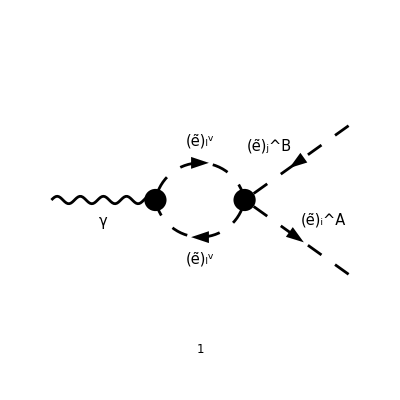

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,1->2,
ExcludeTopologies->{SelfEnergies,Tadpoles}],
{V[1]}->{-S[12,{B,j}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{V[1|2|3],S[1|2|3|4|5|6|13|14],F[11|12]}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
M[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
ChangeDimension->D,
Contract->False,
LorentzIndexNames->{μ,ν},
List->False,
SMP->True,
DropSumOver->True
]
```

(ⅈ e^3 (-2 k+k_1+k_2)^μ ε^μ(p) (2 Conjugate[(USf(2,j)(B,2))] (IndexDelta(i,Gen4) IndexDelta(j,Gen4) Conjugate[(USf(2,i)(Sfe4,1))] (MLE(i) MLE(j) (cos(θ_W))^2 USf(2,i)(A,2) USf(2,j)(Sfe4,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,1) USf(2,j)(Sfe4,2))+IndexDelta(i,j) (Conjugate[(USf(2,Gen4)(Sfe4,1))] (MLE(j) (cos(θ_W))^2 MLE(Gen4) USf(2,j)(A,1) USf(2,Gen4)(Sfe4,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,j)(A,2) USf(2,Gen4)(Sfe4,1))+2 CB^2 m_W^2 (sin(θ_W))^2 USf(2,j)(A,2) USf(2,Gen4)(Sfe4,2) Conjugate[(USf(2,Gen4)(Sfe4,2))])+2 CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) IndexDelta(i,Gen4) IndexDelta(j,Gen4) USf(2,j)(Sfe4,2) Conjugate[(USf(2,i)(Sfe4,2))])+Conjugate[(USf(2,j)(B,1))] (2 IndexDelta(i,Gen4) IndexDelta(j,Gen4) Conjugate[(USf(2,i)(Sfe4,2))] (MLE(i) MLE(j) (cos(θ_W))^2 USf(2,i)(A,1) USf(2,j)(Sfe4,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) USf(2,j)(Sfe4,1))+IndexDelta(i,j) (2 Conjugate[(USf(2,Gen4)(Sfe4,2))] (MLE(j) (cos(θ_W))^2 MLE(Gen4) USf(2,j)(A,2) USf(2,Gen4)(Sfe4,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,j)(A,1) USf(2,Gen4)(Sfe4,2))+CB^2 m_W^2 USf(2,j)(A,1) USf(2,Gen4)(Sfe4,1) Conjugate[(USf(2,Gen4)(Sfe4,1))])+CB^2 m_W^2 USf(2,i)(A,1) IndexDelta(i,Gen4) IndexDelta(j,Gen4) USf(2,j)(Sfe4,1) Conjugate[(USf(2,i)(Sfe4,1))])))/(64 π^4 CB^2 m_W^2 (cos(θ_W))^2 (sin(θ_W))^2 (k^2-m_l_Gen4Sfe4^2).((k-k_1-k_2)^2-m_l_Gen4Sfe4^2))

```mathematica
M[1]=M[0]/ChangeDimension[PolarizationVector[p,μ],D](*Remove polarization vector*)
```

(ⅈ e^3 (-2 k+k_1+k_2)^μ (2 Conjugate[(USf(2,j)(B,2))] (IndexDelta(i,Gen4) IndexDelta(j,Gen4) Conjugate[(USf(2,i)(Sfe4,1))] (MLE(i) MLE(j) (cos(θ_W))^2 USf(2,i)(A,2) USf(2,j)(Sfe4,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,1) USf(2,j)(Sfe4,2))+IndexDelta(i,j) (Conjugate[(USf(2,Gen4)(Sfe4,1))] (MLE(j) (cos(θ_W))^2 MLE(Gen4) USf(2,j)(A,1) USf(2,Gen4)(Sfe4,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,j)(A,2) USf(2,Gen4)(Sfe4,1))+2 CB^2 m_W^2 (sin(θ_W))^2 USf(2,j)(A,2) USf(2,Gen4)(Sfe4,2) Conjugate[(USf(2,Gen4)(Sfe4,2))])+2 CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) IndexDelta(i,Gen4) IndexDelta(j,Gen4) USf(2,j)(Sfe4,2) Conjugate[(USf(2,i)(Sfe4,2))])+Conjugate[(USf(2,j)(B,1))] (2 IndexDelta(i,Gen4) IndexDelta(j,Gen4) Conjugate[(USf(2,i)(Sfe4,2))] (MLE(i) MLE(j) (cos(θ_W))^2 USf(2,i)(A,1) USf(2,j)(Sfe4,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) USf(2,j)(Sfe4,1))+IndexDelta(i,j) (2 Conjugate[(USf(2,Gen4)(Sfe4,2))] (MLE(j) (cos(θ_W))^2 MLE(Gen4) USf(2,j)(A,2) USf(2,Gen4)(Sfe4,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,j)(A,1) USf(2,Gen4)(Sfe4,2))+CB^2 m_W^2 USf(2,j)(A,1) USf(2,Gen4)(Sfe4,1) Conjugate[(USf(2,Gen4)(Sfe4,1))])+CB^2 m_W^2 USf(2,i)(A,1) IndexDelta(i,Gen4) IndexDelta(j,Gen4) USf(2,j)(Sfe4,1) Conjugate[(USf(2,i)(Sfe4,1))])))/(64 π^4 CB^2 m_W^2 (cos(θ_W))^2 (sin(θ_W))^2 (k^2-m_l_Gen4Sfe4^2).((k-k_1-k_2)^2-m_l_Gen4Sfe4^2))

```mathematica
M[2]=M[1]//FCE//Collect2[#,{FVD[_,μ],FAD[__]},Factoring->FullSimplify,IsolateNames->KK]&
```

(ⅈ KK(670) (-2 k+k_1+k_2)^μ)/(64 (k^2-m_l_Gen4Sfe4^2).((k-k_1-k_2)^2-m_l_Gen4Sfe4^2))

```mathematica
M[3]=M[2]//ReplaceAll[#,{k1+k2->p,-k1-k2->-p}]&
```

(ⅈ KK(670) (p-2 k)^μ)/(64 (k^2-m_l_Gen4Sfe4^2).((k-p)^2-m_l_Gen4Sfe4^2))

```mathematica
M[4]=M[3]//TID[#,k,UsePaVeBasis->True]&
```

1/64 π^2 KK(670) p^μ B_0(p^2,m_l_Gen4Sfe4^2,m_l_Gen4Sfe4^2)+(ⅈ KK(670) p^μ)/(64 (k^2-m_l_Gen4Sfe4^2).((k-p)^2-m_l_Gen4Sfe4^2))

Proportional to p^μ as expected

## Finite integrations for radiation

```mathematica
$Assumptions={
xm∈Reals,
xp∈Reals,
-1<xm<xp<1,
λ∈PositiveReals
};
```

```mathematica
xpmRules={
xm->-(β1-β2)-Sqrt[λ],
xp->-(β1-β2)+Sqrt[λ]
};
fromλRules={
λ->1+β1^2+β2^2-2(β1+β2)-2β1 β2
};
toλRules={
β1^2-2(β2+1)β1+(β2-1)^2->λ,
(β1-1)^2+β2^2-2(β1+1)β2->λ
};
logRules={
-((-1+β1+β2+Sqrt[λ])/(1-β1-β2+Sqrt[λ]))->(Sqrt[λ]-1+β1+β2)^2/(4β1 β2),
(-β1+β2-Sqrt[λ]+1)/(-β1+β2+Sqrt[λ]+1)->(β1-β2+Sqrt[λ]-1)^2/(4β2),
(β1-β2-Sqrt[λ]+1)/(β1-β2+Sqrt[λ]+1)->(Sqrt[λ]-1-β1+β2)^2/(4β1),
(β1-β2+Sqrt[λ]+1)/(β1-β2-Sqrt[λ]+1)->4β1/(-β1+β2+Sqrt[λ]-1)^2,
(-β1+β2+Sqrt[λ]+1)/(-β1+β2-Sqrt[λ]+1)->4β2/(β1-β2+Sqrt[λ]-1)^2,
(β1+β2-Sqrt[λ]-1)/(β1+β2+Sqrt[λ]-1)->(β1+β2-Sqrt[λ]-1)^2/(4β1 β2)
};
```

```mathematica
(* Proof of logRules (remove semicolons) *)
-((-1+β1+β2+Sqrt[λ])/(1-β1-β2+Sqrt[λ]));
((%//Numerator)(-β1-β2-Sqrt[λ]+1))/((%//Denominator)(-β1-β2-Sqrt[λ]+1)//Expand//ReplaceAll[#,fromλRules]&//Simplify);
(**)
(-β1+β2-Sqrt[λ]+1)/(-β1+β2+Sqrt[λ]+1);
((%//Numerator)(-β1+β2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&)/((%//Denominator)(-β1+β2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify);
(**)
(β1-β2-Sqrt[λ]+1)/(β1-β2+Sqrt[λ]+1);
((%//Numerator)(β1-β2-Sqrt[λ]+1))/((%//Denominator)(β1-β2-Sqrt[λ]+1)//Expand//ReplaceAll[#,fromλRules]&//Simplify);
(**)
(β1-β2+Sqrt[λ]+1)/(β1-β2-Sqrt[λ]+1);
((%//Numerator)(β1-β2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify)/((%//Denominator)(β1-β2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&);
(**)
(-β1+β2+Sqrt[λ]+1)/(-β1+β2-Sqrt[λ]+1);
((%//Numerator)(-β1+β2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify)/((%//Denominator)(-β1+β2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&);
(**)
(β1+β2-Sqrt[λ]-1)/(β1+β2+Sqrt[λ]-1);
((%//Numerator)(β1+β2-Sqrt[λ]-1)//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&)/((%//Denominator)(β1+β2-Sqrt[λ]-1)//ReplaceAll[#,fromλRules]&//FullSimplify);
```

### Divergent part

```mathematica
I1[0]=(xp-x)(x-xm)/((1+x)^2(1-x)^2)
I1[1]=I1[0]//Integrate2[#,{x,xm,xp}]&
I1[2]=I1[1]//ReplaceAll[#,Integrate3->Integrate]&//FRH
I1[3]=I1[2]//FullSimplify//ReplaceRepeated[#,Union[xpmRules,fromλRules]]&//FullSimplify//ReplaceAll[#,toλRules]&//ReplaceAll[#,logRules]&
```

((x-x^-) (x^+-x))/((1-x)^2 (x+1)^2)

1/4 x^- Hold[Integrate3][1/(1-x)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][1/(1-x)^2,{x,x^-,x^+}]+1/4 x^+ Hold[Integrate3][1/(1-x)^2,{x,x^-,x^+}]-1/4 Hold[Integrate3][1/(1-x)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][1/(1-x),{x,x^-,x^+}]+1/4 Hold[Integrate3][1/(1-x),{x,x^-,x^+}]-1/4 x^- Hold[Integrate3][1/(x+1)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][1/(x+1)^2,{x,x^-,x^+}]-1/4 x^+ Hold[Integrate3][1/(x+1)^2,{x,x^-,x^+}]-1/4 Hold[Integrate3][1/(x+1)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][1/(x+1),{x,x^-,x^+}]+1/4 Hold[Integrate3][1/(x+1),{x,x^-,x^+}]

1/4 (-1/(x^--1)-1/(1-x^+))+1/4 x^- (1/(x^--1)+1/(1-x^+))-1/4 x^- (1/(x^--1)+1/(1-x^+)) x^++1/4 (1/(x^--1)+1/(1-x^+)) x^+-1/4 x^- (1/(x^-+1)-1/(x^++1))-1/4 x^- x^+ (1/(x^-+1)-1/(x^++1))-1/4 x^+ (1/(x^-+1)-1/(x^++1))+1/4 (1/(x^++1)-1/(x^-+1))-1/4 x^- x^+ log((x^--1)/(x^+-1))+1/4 log((x^--1)/(x^+-1))-1/4 x^- x^+ log((x^++1)/(x^-+1))+1/4 log((x^++1)/(x^-+1))

1/2 (β_1+β_2-1) log((β_1+β_2+√λ-1)^2/(4 β_1 β_2))-√λ

### Finite δ(1-z) part

```mathematica
I2[0]=(xp-x)(x-xm)/((1+x)^2(1-x)^2)Log[(xp-x)(x-xm)]
I2[1]=I2[0]//Integrate2[#,{x,xm,xp}]&
I2[2]=I2[1]//ReplaceAll[#,Integrate3->Integrate]&//FRH
```

((x-x^-) (x^+-x) log((x-x^-) (x^+-x)))/((1-x)^2 (x+1)^2)

1/4 x^- Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x)^2,{x,x^-,x^+}]+1/4 x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x)^2,{x,x^-,x^+}]-1/4 Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x),{x,x^-,x^+}]+1/4 Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x),{x,x^-,x^+}]-1/4 x^- Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1)^2,{x,x^-,x^+}]-1/4 x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1)^2,{x,x^-,x^+}]-1/4 Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1),{x,x^-,x^+}]+1/4 Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1),{x,x^-,x^+}]

-1/4 x^- x^+ (-2(x^--1)/(x^+-1)+2(x^+-1)/(x^--1)+log((x^--1)/(x^+-1)) (log((x^--1) (x^+-1))-ⅈ π))+1/4 (-2(x^--1)/(x^+-1)+2(x^+-1)/(x^--1)+log((x^--1)/(x^+-1)) (log((x^--1) (x^+-1))-ⅈ π))-1/4 x^- x^+ (2(x^-+1)/(x^++1)-2(x^++1)/(x^-+1)-log((x^-+1)/(x^++1)) (log(x^-+1)+log(x^++1)-ⅈ π))+1/4 (2(x^-+1)/(x^++1)-2(x^++1)/(x^-+1)-log((x^-+1)/(x^++1)) (log(x^-+1)+log(x^++1)-ⅈ π))-(x^- x^+ ((x^-+x^+-2) log((x^--1)/(x^+-1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^--1) (x^+-1))+(x^+ ((x^-+x^+-2) log((x^--1)/(x^+-1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^--1) (x^+-1))+(x^- ((x^-+x^+-2) log((x^--1)/(x^+-1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^--1) (x^+-1))-((x^-+x^+-2) log((x^--1)/(x^+-1))+2 (x^+-x^-) log(x^+-x^-))/(4 (x^--1) (x^+-1))-(x^- x^+ ((x^-+x^++2) log((x^-+1)/(x^++1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^-+1) (x^++1))-(x^+ ((x^-+x^++2) log((x^-+1)/(x^++1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^-+1) (x^++1))-(x^- ((x^-+x^++2) log((x^-+1)/(x^++1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^-+1) (x^++1))-((x^-+x^++2) log((x^-+1)/(x^++1))+2 (x^+-x^-) log(x^+-x^-))/(4 (x^-+1) (x^++1))

```mathematica
I2[3]=I2[2]//FullSimplify//ReplaceRepeated[#,Union[xpmRules,fromλRules]]&//FullSimplify//ReplaceAll[#,toλRules]&//Simplify//ReplaceAll[#,logRules]&
```

1/8 (6 (β_1+β_2-1) log^2(-β_1+β_2-√λ+1)-2 (β_1+β_2-1) log^2((4 β_1)/(-β_1+β_2+√λ-1)^2)-2 (β_1+β_2-1) log^2(-β_1+β_2+√λ+1)-4 (β_1+β_2-1) log(-β_1+β_2+√λ+1) log(-β_1+β_2-√λ+1)+4 (β_1-β_2) log(((β_1-β_2+√λ)^2-1)/((-β_1+β_2+√λ)^2-1))+4 log((β_1+β_2-√λ-1)^2/(4 β_1 β_2))+4 ⅈ π (2 β_1+2 β_2-1) log((4 β_2)/(β_1-β_2+√λ-1)^2)+4 ⅈ π log((β_1-β_2+√λ-1)^2/(4 β_2))-4 (β_1+β_2-1) log(4 β_1) log((4 β_1)/(-β_1+β_2+√λ-1)^2)-8 (β_1-β_2+√λ) log(2 √λ)-8 (-β_1+β_2+√λ) log(2 √λ)+8 (β_1+β_2-1) 2(4 β_2)/(β_1-β_2+√λ-1)^2-8 (β_1+β_2-1) 2(-β_1+β_2+√λ-1)^2/(4 β_1))

```mathematica
I2[4]=I2[3]//Collect2[#,{Log},Factoring->FullSimplify,IsolateNames->KK]&
```

1/2 log((β_1+β_2-√λ-1)^2/(4 β_1 β_2))+1/2 ⅈ π log((β_1-β_2+√λ-1)^2/(4 β_2))+3/4 KK(612) log^2(-β_1+β_2-√λ+1)+1/4 KK(611) log^2((4 β_1)/(-β_1+β_2+√λ-1)^2)+1/4 KK(611) log^2(-β_1+β_2+√λ+1)+1/2 KK(611) log(-β_1+β_2+√λ+1) log(-β_1+β_2-√λ+1)+1/2 KK(613) log(((β_1-β_2+√λ)^2-1)/((-β_1+β_2+√λ)^2-1))+1/2 ⅈ KK(610) log((4 β_2)/(β_1-β_2+√λ-1)^2)+1/2 KK(611) log(4 β_1) log((4 β_1)/(-β_1+β_2+√λ-1)^2)-2 KK(614) log(2 √λ)+KK(639)

## 06.03

### Check diagram structure for hadron-side contribution

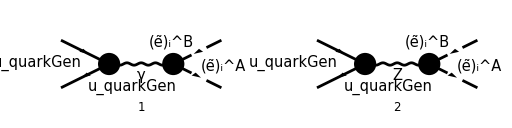

```mathematica
diags[0]=InsertFields[
CreateTopologies[0,2->2],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1|2|3|4|5|6]}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
MLO[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
ChangeDimension->D,
LorentzIndexNames->{μ,ν},
UndoChiralSplittings->True,
DropSumOver->True,
List->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

{(ⅈ e (k_1-k_2)^ν g^μν IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(φ(p_1)))/(k_1+k_2)^2,-((ⅈ e (k_1-k_2)^ν g^μν (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e γ^μ.(γ̄)^6 δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(ⅈ e γ^μ.(γ̄)^7 δ_Col1Col2 (4 (sin(θ_W))^2-3))/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2)))}

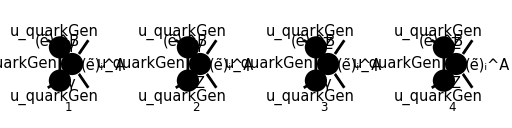

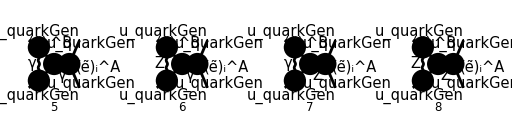

```mathematica
diags[1]=InsertFields[
CreateTopologies[1,2->2,
ExcludeTopologies->{Tadpoles,SelfEnergies}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],(*Higgs*)
F[11|12],(*Electroweakinos*)
S[11|12],(*Sleptons*)
S[13|14],(*Squarks*)
V[3](*W-bosons*)
}
];
Paint[
diags[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
MLO[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
ChangeDimension->D,
LorentzIndexNames->{μ,ν},
UndoChiralSplittings->True,
DropSumOver->True,
List->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

{(ⅈ e (k_1-k_2)^ν g^μν IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(φ(p_1)))/(k_1+k_2)^2,-((ⅈ e (k_1-k_2)^ν g^μν (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e γ^μ.(γ̄)^6 δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(ⅈ e γ^μ.(γ̄)^7 δ_Col1Col2 (4 (sin(θ_W))^2-3))/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2)))}

## 09.03

```mathematica
$Assumptions={
0<x<1,
s∈PositiveReals,
d∈PositiveReals
};
```

```mathematica
(-x y s)^((d-4)/2)
%//Integrate[#,{y,0,1-x}]&
```

(-s x y)^((d-4)/2)

ConditionalExpression[(2 ⅈ^d (1-x)^(d/2-1) (s x)^(d/2-2))/(d-2), d>2]

```mathematica
1/Gamma[d-1]
%//ReplaceAll[#,d->4-2ϵ]&
%//Series[#,{ϵ,0,2}]&
```

1/(d-1)

1/(3-2 ϵ)

1/2+1/2 (3-2 ℽ) ϵ+1/6 (21-18 ℽ+6 ℽ^2-π^2) ϵ^2+O(ϵ^3)

```mathematica
Gamma[ϵ]//Series[#,{ϵ,0,2}]&
```

1/ϵ-ℽ+1/12 (6 ℽ^2+π^2) ϵ+1/6 ϵ^2 (-ℽ^3-(ℽ π^2)/2+21)+O(ϵ^3)

```mathematica
Gamma[2-ϵ]//Series[#,{ϵ,0,2}]&
```

1+(ℽ-1) ϵ+1/12 (-12 ℽ+6 ℽ^2+π^2) ϵ^2+O(ϵ^3)

```mathematica
1/Gamma[3-2ϵ]//Series[#,{ϵ,0,1}]&
```

1/2+1/2 (3-2 ℽ) ϵ+O(ϵ^2)

```mathematica
integrand=((d-2)/2x y-x-y+1)(-x y s)^((d-6)/2)
%//Integrate[#,{y,0,1-x}]&
%//Integrate[#,{x,0,1}]&
```

(1/2 (d-2) x y-x-y+1) (-s x y)^((d-6)/2)

ConditionalExpression[-(ⅈ^d (1-x)^(d/2-1) ((d-4) (d-2) x+4) (s x)^(d/2-3))/((d-4) (d-2)), d>4]

ConditionalExpression[-(ⅈ^d ((d-8) d+24) s^(d/2-3) d/2-2 d/2)/(2 (d-4) d-1), d>4]

```mathematica
Gamma[ϵ]//Series[#,{ϵ,0,2}]&
```

1/ϵ-ℽ+1/12 (6 ℽ^2+π^2) ϵ+1/6 ϵ^2 (-ℽ^3-(ℽ π^2)/2+21)+O(ϵ^3)

```mathematica
1/Gamma[2-2ϵ]//Series[#,{ϵ,0,2}]&
```

1+(2-2 ℽ) ϵ+(4-4 ℽ+2 ℽ^2-π^2/3) ϵ^2+O(ϵ^3)

```mathematica
Gamma[ϵ]//Series[#,{ϵ,0,1}]&
```

1/ϵ-ℽ+1/12 (6 ℽ^2+π^2) ϵ+O(ϵ^2)

```mathematica
1/(2-2ϵ)//Series[#,{ϵ,0,2}]&
```

1/2+ϵ/2+ϵ^2/2+O(ϵ^3)

```mathematica
(d^2-8d+24)/(2(d-2))//ReplaceAll[#,{d->4-2ϵ}]&//Series[#,{ϵ,0,2}]&
```

2+2 ϵ+3 ϵ^2+O(ϵ^3)

```mathematica
Gamma[-ϵ]//Series[#,{ϵ,0,1}]&
```

-1/ϵ-ℽ+1/12 (-6 ℽ^2-π^2) ϵ+O(ϵ^2)

```mathematica
(d^2-8d+24)/(2(d-2))Gamma[(4-d)/2]Gamma[(d-4)/2]Gamma[d/2]/Gamma[d-2]
%//ReplaceAll[#,{d->4-2ϵ}]&//Series[#,{ϵ,0,0}]&
```

((d^2-8 d+24) (4-d)/2 (d-4)/2 d/2)/(2 (d-2) d-2)

-2/ϵ^2+(2 (ℽ-2))/ϵ+1/6 (-54+24 ℽ-6 ℽ^2+π^2)+O(ϵ^1)

```mathematica
(1/ϵ-EulerGamma+ϵ(EulerGamma^2/2+Pi^2/12))(1/ϵ+EulerGamma+ϵ(EulerGamma^2/2+Pi^2/12))
%//Series[#,{ϵ,0,0}]&
```

((ℽ^2/2+π^2/12) ϵ+1/ϵ-ℽ) ((ℽ^2/2+π^2/12) ϵ+1/ϵ+ℽ)

1/ϵ^2+π^2/6+O(ϵ^1)

```mathematica
(1+ϵ(EulerGamma-1)+ϵ^2(EulerGamma^2/2-EulerGamma+Pi^2/12))(1-2ϵ(EulerGamma-1)+ϵ^2(2EulerGamma^2-4EulerGamma+4-Pi^2/3))
%//Series[#,{ϵ,0,2}]&
```

((4-4 ℽ+2 ℽ^2-π^2/3) ϵ^2-2 (ℽ-1) ϵ+1) ((-ℽ+ℽ^2/2+π^2/12) ϵ^2+(ℽ-1) ϵ+1)

1+(1-ℽ) ϵ+1/4 (8-4 ℽ+2 ℽ^2-π^2) ϵ^2+O(ϵ^3)

```mathematica
(d^2-8d+24)/(2(d-2))Gamma[(4-d)/2]Gamma[(d-4)/2]Gamma[d/2]/Gamma[d-2]
I2=%//ReplaceAll[#,{d->4-2EpsilonIR}]&//Series[#,{EpsilonIR,0,0}]&
```

((d^2-8 d+24) (4-d)/2 (d-4)/2 d/2)/(2 (d-2) d-2)

-2/ε_IR^2+(2 (ℽ-2))/ε_IR+1/6 (-54+24 ℽ-6 ℽ^2+π^2)+O(ε_IR^1)

```mathematica
2Gamma[(4-d)/2]Gamma[d/2]^2/Gamma[d-1]
I1=%//ReplaceAll[#,{d->4-2EpsilonUV}]&//Series[#,{EpsilonUV,0,0}]&
```

(2 (4-d)/2 (d/2)^2)/(d-1)

1/ε_UV+(1-ℽ)+O(ε_UV^1)

```mathematica
I1
```

1/ε_UV+(1-ℽ)+O(ε_UV^1)

```mathematica
I2
```

-2/ε_IR^2+(2 (ℽ-2))/ε_IR+1/6 (-54+24 ℽ-6 ℽ^2+π^2)+O(ε_IR^1)

```mathematica
-(I1+I2)//Normal//FullSimplify
```

(4-2 ℽ)/ε_IR+2/ε_IR^2-1/ε_UV-π^2/6+(ℽ-3) ℽ+8

## 10.03

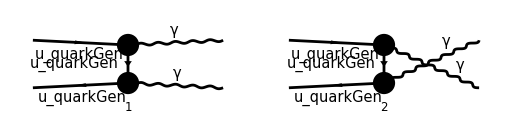

```mathematica
diags[0]=InsertFields[
CreateTopologies[0,2->2],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{V[1],V[1]},
Model->MSSM,
InsertionLevel->{Classes}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

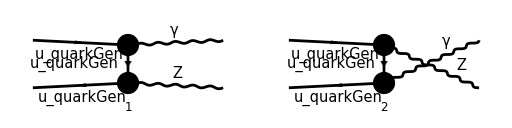

```mathematica
diags[1]=InsertFields[
CreateTopologies[0,2->2],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{V[1],V[2]},
Model->MSSM,
InsertionLevel->{Classes}
];
Paint[
diags[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
Mγ[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k,q},
LorentzIndexNames->{ρ,μ},
ChangeDimension->D,
SMP->True,
List->False,
DropSumOver->True,
UndoChiralSplittings->True
]/.{MQU[quarkGen]->0}
```

((ε^*)^ρ(k) (ε^*)^μ(q) (φ(-p_2)).(-2/3 ⅈ e γ^ρ δ_Col1Col2).(γ·(k-p_2)).(-2/3 ⅈ e γ^μ).(φ(p_1)))/(p_2-k)^2+((ε^*)^ρ(k) (ε^*)^μ(q) (φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(γ·(q-p_2)).(-2/3 ⅈ e γ^ρ).(φ(p_1)))/(p_2-q)^2

```mathematica
Mγ[1]=3/2SMP["e_Q"]Mγ[0]/(ChangeDimension[ComplexConjugate[PolarizationVector[k,ρ]],D] ChangeDimension[ComplexConjugate[PolarizationVector[q,μ]],D])//FullSimplify
```

3/2 e_Q (((φ(-p_2)).(-2/3 ⅈ e γ^ρ δ_Col1Col2).(γ·(k-p_2)).(-2/3 ⅈ e γ^μ).(φ(p_1)))/(p_2-k)^2+((φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(γ·(q-p_2)).(-2/3 ⅈ e γ^ρ).(φ(p_1)))/(p_2-q)^2)

```mathematica
GA[α,β,γ,δ,ϵ,ζ,η,θ,5]
%//DiracTrace
%//DiracSimplify//FCE//Collect2[#,{LC},IsolateNames->KK]&
```

(γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^ϵ.(γ̄)^ζ.(γ̄)^η.(γ̄)^θ.(γ̄)^5

tr((γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^ϵ.(γ̄)^ζ.(γ̄)^η.(γ̄)^θ.(γ̄)^5)

-4 ⅈ KK(128) (ϵ̄)^αβγδ-4 ⅈ KK(142) (ϵ̄)^αβγζ+4 ⅈ KK(136) (ϵ̄)^αβγη-4 ⅈ KK(143) (ϵ̄)^αβγθ+4 ⅈ KK(137) (ϵ̄)^αβγϵ-4 ⅈ KK(138) (ϵ̄)^αδϵζ+4 ⅈ KK(135) (ϵ̄)^αδϵη-4 ⅈ KK(141) (ϵ̄)^αδϵθ-4 ⅈ KK(134) (ϵ̄)^αζηθ+4 ⅈ KK(127) (ϵ̄)^βδϵζ-4 ⅈ KK(125) (ϵ̄)^βδϵη+4 ⅈ KK(129) (ϵ̄)^βδϵθ+4 ⅈ KK(140) (ϵ̄)^βζηθ-4 ⅈ KK(131) (ϵ̄)^γδϵζ+4 ⅈ KK(133) (ϵ̄)^γδϵη-4 ⅈ KK(139) (ϵ̄)^γδϵθ-4 ⅈ KK(132) (ϵ̄)^γζηθ+4 ⅈ KK(130) (ϵ̄)^δζηθ-4 ⅈ KK(126) (ϵ̄)^ϵζηθ

```mathematica
GA[α,β,γ,δ,ϵ,ζ,5]
%//DiracTrace
%//DiracSimplify//FCE//Collect2[#,{LC},IsolateNames->KK]&
```

(γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^ϵ.(γ̄)^ζ.(γ̄)^5

tr((γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^ϵ.(γ̄)^ζ.(γ̄)^5)

-4 ⅈ KK(161) (ϵ̄)^αβγδ-4 ⅈ KK(162) (ϵ̄)^αβγζ+4 ⅈ KK(159) (ϵ̄)^αβγϵ-4 ⅈ KK(163) (ϵ̄)^αδϵζ+4 ⅈ KK(158) (ϵ̄)^βδϵζ-4 ⅈ KK(160) (ϵ̄)^γδϵζ

```mathematica
GA[α,β,γ,δ,5]
%//DiracTrace
%//DiracSimplify//FCE//Collect2[#,{LC},IsolateNames->KK]&
```

(γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^5

tr((γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^5)

-4 ⅈ (ϵ̄)^αβγδ

```mathematica
GA[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8,μ9,μ10,5]
%//DiracTrace
%//DiracSimplify//FCE//Collect2[#,{LC},IsolateNames->KK]&
```

(γ̄)^μ1.(γ̄)^μ2.(γ̄)^μ3.(γ̄)^μ4.(γ̄)^μ5.(γ̄)^μ6.(γ̄)^μ7.(γ̄)^μ8.(γ̄)^μ9.(γ̄)^μ10.(γ̄)^5

tr((γ̄)^μ1.(γ̄)^μ2.(γ̄)^μ3.(γ̄)^μ4.(γ̄)^μ5.(γ̄)^μ6.(γ̄)^μ7.(γ̄)^μ8.(γ̄)^μ9.(γ̄)^μ10.(γ̄)^5)

-4 ⅈ KK(220) (ϵ̄)^μ1μ10μ2μ3-4 ⅈ KK(214) (ϵ̄)^μ1μ10μ4μ5-4 ⅈ KK(210) (ϵ̄)^μ1μ10μ6μ7-4 ⅈ KK(222) (ϵ̄)^μ1μ10μ8μ9-4 ⅈ KK(229) (ϵ̄)^μ1μ2μ3μ4+4 ⅈ KK(239) (ϵ̄)^μ1μ2μ3μ5-4 ⅈ KK(219) (ϵ̄)^μ1μ2μ3μ6+4 ⅈ KK(235) (ϵ̄)^μ1μ2μ3μ7-4 ⅈ KK(204) (ϵ̄)^μ1μ2μ3μ8+4 ⅈ KK(225) (ϵ̄)^μ1μ2μ3μ9-4 ⅈ KK(196) (ϵ̄)^μ1μ4μ5μ6+4 ⅈ KK(215) (ϵ̄)^μ1μ4μ5μ7-4 ⅈ KK(231) (ϵ̄)^μ1μ4μ5μ8+4 ⅈ KK(192) (ϵ̄)^μ1μ4μ5μ9-4 ⅈ KK(242) (ϵ̄)^μ1μ6μ7μ8+4 ⅈ KK(226) (ϵ̄)^μ1μ6μ7μ9-4 ⅈ KK(232) (ϵ̄)^μ10μ2μ4μ5-4 ⅈ KK(234) (ϵ̄)^μ10μ2μ6μ7-4 ⅈ KK(238) (ϵ̄)^μ10μ2μ8μ9+4 ⅈ KK(203) (ϵ̄)^μ10μ3μ4μ5+4 ⅈ KK(241) (ϵ̄)^μ10μ3μ6μ7+4 ⅈ KK(236) (ϵ̄)^μ10μ3μ8μ9-4 ⅈ KK(237) (ϵ̄)^μ10μ4μ6μ7-4 ⅈ KK(199) (ϵ̄)^μ10μ4μ8μ9+4 ⅈ KK(227) (ϵ̄)^μ10μ5μ6μ7+4 ⅈ KK(194) (ϵ̄)^μ10μ5μ8μ9-4 ⅈ KK(193) (ϵ̄)^μ10μ6μ8μ9+4 ⅈ KK(224) (ϵ̄)^μ10μ7μ8μ9+4 ⅈ KK(200) (ϵ̄)^μ2μ4μ5μ6-4 ⅈ KK(233) (ϵ̄)^μ2μ4μ5μ7+4 ⅈ KK(207) (ϵ̄)^μ2μ4μ5μ8-4 ⅈ KK(211) (ϵ̄)^μ2μ4μ5μ9+4 ⅈ KK(230) (ϵ̄)^μ2μ6μ7μ8-4 ⅈ KK(206) (ϵ̄)^μ2μ6μ7μ9-4 ⅈ KK(228) (ϵ̄)^μ3μ4μ5μ6+4 ⅈ KK(198) (ϵ̄)^μ3μ4μ5μ7-4 ⅈ KK(208) (ϵ̄)^μ3μ4μ5μ8+4 ⅈ KK(240) (ϵ̄)^μ3μ4μ5μ9-4 ⅈ KK(223) (ϵ̄)^μ3μ6μ7μ8+4 ⅈ KK(213) (ϵ̄)^μ3μ6μ7μ9+4 ⅈ KK(221) (ϵ̄)^μ4μ6μ7μ8-4 ⅈ KK(202) (ϵ̄)^μ4μ6μ7μ9-4 ⅈ KK(217) (ϵ̄)^μ5μ6μ7μ8+4 ⅈ KK(218) (ϵ̄)^μ5μ6μ7μ9

## 11.03

```mathematica
1/Gamma[(d-1)/2]
%//ReplaceAll[#,{d->4-2ϵ}]&
%//Series[#,{ϵ,0,1}]&
```

1/((d-1)/2)

1/(1/2 (3-2 ϵ))

2/(√π)+(2 ϵ 03/2)/(√π)+O(ϵ^2)

```mathematica
Gamma[(d-1)/2]
%//ReplaceAll[#,{d->4-2ϵ}]&
%//Series[#,{ϵ,0,1}]&
```

(d-1)/2

1/2 (3-2 ϵ)

(√π)/2-1/2 ϵ (√π 03/2)+O(ϵ^2)

```mathematica
HarmonicNumber[2]
```

3/2

## 12.03

```mathematica
S[μ_,ν_]:=1/t GAD[μ].GSD[p1-k].GAD[ν]-1/u GAD[ν].GSD[p2-k].GAD[μ]
```

```mathematica
GSD[p2].S[μ,ν].GSD[p1].S[σ,ρ]
```

(γ·p_2).((γ^μ.(γ·(p_1-k)).γ^ν)/t-(γ^ν.(γ·(p_2-k)).γ^μ)/u).(γ·p_1).((γ^σ.(γ·(p_1-k)).γ^ρ)/t-(γ^ρ.(γ·(p_2-k)).γ^σ)/u)

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,k,q,0,0,0,Q];
```

```mathematica
DiracTrace[GSD[p2].GAD[μ].GSD[p1-k].GAD[ν].GSD[p1].GAD[μ].GSD[p2-k].GAD[ν]]
%//DiracSimplify//FullSimplify
%//TrickMandelstam[#,{s,t,u,Q^2}]&//FullSimplify
```

tr((γ·p_2).γ^μ.(γ·(p_1-k)).γ^ν.(γ·p_1).γ^μ.(γ·(p_2-k)).γ^ν)

-2 (D-2) ((D-4) t u+2 s^2-2 s (t+u))

-2 (D-2) (u (D t+4 u)-2 Q^2 (s+2 u)+4 s^2+4 s u)

```mathematica
GAD[μ].GAD[ν].GAD[λ].GAD[μ]
%//DiracSimplify//Simplify
```

γ^μ.γ^ν.γ^λ.γ^μ

(D-4) γ^ν.γ^λ+4 g^λν

```mathematica
GAD[μ].GAD[ν].GAD[λ].GAD[ρ].GAD[μ]
%//DiracSimplify//Simplify
```

γ^μ.γ^ν.γ^λ.γ^ρ.γ^μ

-2 γ^ρ.γ^λ.γ^ν-((D-4) γ^ν.γ^λ.γ^ρ)

## 13.03

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,k,q,0,0,0,Q];
```

```mathematica
DiracTrace[GSD[p1].GAD[μ].GSD[p1-k].GAD[ν].GSD[p2].GAD[μ].GSD[p2-k].GAD[ν]]
%//DiracSimplify//FullSimplify
%//TrickMandelstam[#,{s,t,u,Q^2}]&//FullSimplify
```

tr((γ·p_1).γ^μ.(γ·(p_1-k)).γ^ν.(γ·p_2).γ^μ.(γ·(p_2-k)).γ^ν)

-2 (D-2) ((D-4) t u+2 s^2-2 s (t+u))

-2 (D-2) (u (D t+4 u)-2 Q^2 (s+2 u)+4 s^2+4 s u)

```mathematica
DiracTrace[GSD[p1].GAD[μ].GSD[p1-k].GAD[ν].GSD[p2].GAD[μ].GSD[p2-k].GAD[ν]]
DiracTrace[GSD[p2].GAD[μ].GSD[p1-k].GAD[ν].GSD[p1].GAD[μ].GSD[p2-k].GAD[ν]]
FCCompareResults[{%//DiracSimplify},{%%//DiracSimplify}]
```

tr((γ·p_1).γ^μ.(γ·(p_1-k)).γ^ν.(γ·p_2).γ^μ.(γ·(p_2-k)).γ^ν)

tr((γ·p_2).γ^μ.(γ·(p_1-k)).γ^ν.(γ·p_1).γ^μ.(γ·(p_2-k)).γ^ν)

Check of the results: The results agree.

True

```mathematica
GSD[p1].GAD[μ].GSD[p1-k].GAD[ν].GSD[p2].GAD[μ].GSD[p2-k].GAD[ν]
GSD[p1].GAD[μ].GSD[p2-k].GAD[ν].GSD[p2].GAD[μ].GSD[p1-k].GAD[ν]
FCCompareResults[{%//DiracSimplify},{%%//DiracSimplify}]
```

(γ·p_1).γ^μ.(γ·(p_1-k)).γ^ν.(γ·p_2).γ^μ.(γ·(p_2-k)).γ^ν

(γ·p_1).γ^μ.(γ·(p_2-k)).γ^ν.(γ·p_2).γ^μ.(γ·(p_1-k)).γ^ν

Check of the results: The results disagree.

False

```mathematica
FCClearScalarProducts[];
```

```mathematica
DiracTrace[GSD[p1].GAD[μ].GSD[p1-k].GAD[ν].GSD[p2].GAD[μ].GSD[p2-k].GAD[ν]]
DiracTrace[GSD[p1].GAD[μ].GSD[p2-k].GAD[ν].GSD[p2].GAD[μ].GSD[p1-k].GAD[ν]]
FCCompareResults[{%//DiracSimplify},{%%//DiracSimplify}]
```

tr((γ·p_1).γ^μ.(γ·(p_1-k)).γ^ν.(γ·p_2).γ^μ.(γ·(p_2-k)).γ^ν)

tr((γ·p_1).γ^μ.(γ·(p_2-k)).γ^ν.(γ·p_2).γ^μ.(γ·(p_1-k)).γ^ν)

Check of the results: The results agree.

True

```mathematica
(2Pi)^d DeltaFunction[k+1-p1-p2]diff^(d-1)q
```

```mathematica
Gamma[1-ϵ]//Series[#,{ϵ,0,2}]&
-ϵ Gamma[-ϵ]//Series[#,{ϵ,0,2}]&
```

1+ℽ ϵ+1/12 (6 ℽ^2+π^2) ϵ^2+O(ϵ^3)

1+ℽ ϵ+1/12 (6 ℽ^2+π^2) ϵ^2+O(ϵ^3)

## 16.03

```mathematica
Gamma[1-ϵ]/Gamma[1-2ϵ]
%//Series[#,{ϵ,0,2}]&
```

(1-ϵ)/(1-2 ϵ)

1-ℽ ϵ+1/4 (2 ℽ^2-π^2) ϵ^2+O(ϵ^3)

```mathematica
1/(1-2ϵ)
%//Series[#,{ϵ,0,2}]&
```

1/(1-2 ϵ)

1+2 ϵ+4 ϵ^2+O(ϵ^3)

## 17.03

```mathematica
C0[0,s,0,0,0,0]
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

C_0(0,s,0,0,0,0)

-(-log(-μ^2/s)+ℽ-log(4 π))/(s ε_IR)+1/(s ε_IR^2)+(6 log^2(-μ^2/s)+12 log(4 π) log(-μ^2/s)-12 ℽ log(-μ^2/s)-π^2+6 ℽ^2+6 log^2(4 π)-12 ℽ log(4 π))/(12 s)

```mathematica
(-z)^ϵ Gamma[ϵ]Gamma[2-ϵ]/(2(1-2ϵ))
%//Series[#,{ϵ,0,0}]&
```

((-z)^ϵ 2-ϵ ϵ)/(2 (1-2 ϵ))

1/(2 ϵ)+1/2 (log(-z)+1)+O(ϵ^1)

```mathematica
(-z)^ϵ Gamma[ϵ](ϵ/(2(1-ϵ)(1-2ϵ))Gamma[2-ϵ]+Gamma[1-ϵ]/(1-2ϵ)+2Gamma[1-ϵ]/(1-ϵ)+Gamma[1-ϵ]/ϵ)
%//Series[#,{ϵ,0,0}]&
```

(-z)^ϵ ((1-ϵ)/(1-2 ϵ)+(2 1-ϵ)/(1-ϵ)+(1-ϵ)/ϵ+(ϵ 2-ϵ)/(2 (1-2 ϵ) (1-ϵ))) ϵ

1/ϵ^2+(log(-z)+3)/ϵ+1/6 (3 log^2(-z)+18 log(-z)+π^2+27)+O(ϵ^1)

```mathematica
Log[-z]//Assuming[z∈PositiveReals,#]&
```

log(-z)

```mathematica
Assuming[z∈PositiveReals,Re[Log[-z]^2]+I Im[Log[-z]^2]//FullSimplify//Expand]
```

log^2(z)+2 ⅈ π log(z)-π^2

```mathematica
27/6
```

9/2

```mathematica
C0[0,s,0,0,0,0]
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

C_0(0,s,0,0,0,0)

-(-log(-μ^2/s)+ℽ-log(4 π))/(s ε_IR)+1/(s ε_IR^2)+(6 log^2(-μ^2/s)+12 log(4 π) log(-μ^2/s)-12 ℽ log(-μ^2/s)-π^2+6 ℽ^2+6 log^2(4 π)-12 ℽ log(4 π))/(12 s)

```mathematica
FCClearScalarProducts[];
SPD[p1]=0;
SPD[p2]=0;
SPD[p1,p2]=s/2;
```

```mathematica
SpinorVBarD[p2,0].GAD[ρ].GSD[k-p2].GAD[μ].GSD[k+p1].GAD[ρ].SpinorUD[p1,0] FAD[k,k+p1,k-p2]
%//DiracSimplify//FullSimplify
%//TID[#,k,ToPaVe->True]&//Collect2[#,{A0,B0,C0},Factoring->DiracSimplify,IsolateNames->KK]&
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
Γμ=%//FRH//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&
```

(v̄(p_2).γ^ρ.(γ·(k-p_2)).γ^μ.(γ·(k+p_1)).γ^ρ.u(p_1))/(k^2.(k+p_1)^2.(k-p_2)^2)

1/(k^2.(k+p_1)^2.(k-p_2)^2)(((D-2) k^2-2 (-2 (k·p_1)+2 (k·p_2)+s)) (φ(-p_2)).γ^μ.(φ(p_1))-2 ((D-2) k^μ+2 (p_1^μ-p_2^μ)) (φ(-p_2)).(γ·k).(φ(p_1)))

KK(14353) B_0(s,0,0)+4 ⅈ KK(14304) B_0(0,0,0)-2 ⅈ KK(14863) C_0(0,0,s,0,0,0)

-(2 ⅈ (KK(14863) log(-μ^2/s)+2 KK(14304) s-ℽ KK(14863)+KK(14863) log(4 π)))/(s ε_IR)-(2 ⅈ KK(14863))/(s ε_IR^2)-1/(6 s)(6 ⅈ KK(14863) log^2(-μ^2/s)-12 ⅈ ℽ KK(14863) log(-μ^2/s)+12 ⅈ KK(14863) log(4 π) log(-μ^2/s)-6 KK(14353) s log(-(4 π μ^2)/s)+6 ℽ KK(14353) s-12 KK(14353) s-ⅈ π^2 KK(14863)+6 ⅈ ℽ^2 KK(14863)+6 ⅈ KK(14863) log^2(4 π)-12 ⅈ ℽ KK(14863) log(4 π))+(KK(14353)+4 ⅈ KK(14304))/ε_UV

-(2 ⅈ KK(14304))/ε_IR^2+(2 ⅈ KK(16725))/ε_IR+(ⅈ KK(16723))/ε_UV+1/6 ⅈ KK(16730)

```mathematica
KK[14304]
KK[16725]//FRH
KK[16723]//FRH
KK[16730]//FRH
```

π^2 (φ(-p_2)).γ^μ.(φ(p_1))

π^2 (-log(-(4 π μ^2)/s)+ℽ-2) (φ(-p_2)).γ^μ.(φ(p_1))

π^2 (D-3) (φ(-p_2)).γ^μ.(φ(p_1))

π^2 (6 (D+2 ℽ-7) log(-(4 π μ^2)/s)-6 (ℽ-2) D-6 log(-μ^2/s) log(-(16 π^2 μ^2)/s)+π^2-6 (ℽ-7) ℽ-84-6 log^2(4 π)) (φ(-p_2)).γ^μ.(φ(p_1))

```mathematica
-I SMP["e"]^2SMP["e_Q"]^2 Γμ (SpinorUBarD[p1,0].GAD[μ].SpinorVD[p2,0])//FRH//FermionSpinSum[#,ExtraFactor->1/(4SUNN)]&//DiracSimplify//FullSimplify
```

1/(12 N ε_IR^2 ε_UV)π^2 (D-2) e^2 s e_Q^2 (6 ε_IR ε_UV ((2-(D+2 ℽ-7) ε_IR) log(-(4 π μ^2)/s)+ε_IR log(-μ^2/s) log(-(16 π^2 μ^2)/s))+ε_IR^2 (6 D ((ℽ-2) ε_UV-1)+(84+6 (ℽ-7) ℽ-π^2+6 log^2(4 π)) ε_UV+18)-12 (ℽ-2) ε_IR ε_UV+12 ε_UV)

```mathematica
$Assumptions={ϵ>0};
```

```mathematica
x^(-ϵ)y^(-ϵ)
Integrate[%,{y,0,1-x}]
Integrate[%,{x,0,1}]
```

x^-ϵ y^-ϵ

ConditionalExpression[((1-x)^(1-ϵ) x^-ϵ)/(1-ϵ), ϵ<1]

ConditionalExpression[-(√π 4^(ϵ-1) 1-ϵ)/((ϵ-1) 3/2-ϵ), ϵ<1]

```mathematica
$Assumptions={ϵ<0};
```

```mathematica
(1-ϵ)x^(-ϵ)y^(-ϵ)-x^(-ϵ)y^(-1-ϵ)-x^(-1-ϵ)y^(-ϵ)+x^(-1-ϵ)y^(-1-ϵ)
Integrate[%,{y,0,1-x}]//ExpandAll2
```

x^(-ϵ-1) y^(-ϵ-1)-x^(-ϵ-1) y^-ϵ-x^-ϵ y^(-ϵ-1)+(1-ϵ) x^-ϵ y^-ϵ

(x-1)^2 x (-((x-1) x))^(-ϵ-1)+((x-1)^2 (-((x-1) x))^(-ϵ-1))/((ϵ-1) ϵ)

```mathematica
(-z)^ϵ Gamma[ϵ]1/(2(1-2ϵ))Gamma[2-ϵ]
%//Series[#,{ϵ,0,0}]&
```

((-z)^ϵ 2-ϵ ϵ)/(2 (1-2 ϵ))

1/(2 ϵ)+1/2 (log(-z)+1)+O(ϵ^1)

```mathematica
(-z)^ϵ Gamma[ϵ](ϵ/(2(1-ϵ)(1-2ϵ))Gamma[2-ϵ]+Gamma[1-ϵ]/(1-2ϵ)-2ϵ Gamma[1-ϵ]+Gamma[1-ϵ]/ϵ)
%//Series[#,{ϵ,0,0}]&
```

(-z)^ϵ (-2 ϵ 1-ϵ+(1-ϵ)/(1-2 ϵ)+(1-ϵ)/ϵ+(ϵ 2-ϵ)/(2 (1-2 ϵ) (1-ϵ))) ϵ

1/ϵ^2+(log(-z)+1)/ϵ+1/6 (3 log^2(-z)+6 log(-z)+π^2+3)+O(ϵ^1)

```mathematica
1/Gamma[2-ϵ]
%//Series[#,{ϵ,0,1}]&
```

1/(2-ϵ)

1+(1-ℽ) ϵ+O(ϵ^2)

```mathematica
B0[m^2,0,m^2]//PaXEvaluateUVIRSplit
```

log(μ^2/(π m^2))+1/ε_UV-ℽ+2

```mathematica
(-z)^ϵ(1/(2(1-2ϵ))Gamma[ϵ]Gamma[2-ϵ])
%//Series[#,{ϵ,0,0}]&
```

((-z)^ϵ 2-ϵ ϵ)/(2 (1-2 ϵ))

1/(2 ϵ)+1/2 (log(-z)+1)+O(ϵ^1)

```mathematica
(-z)^ϵ Gamma[ϵ](ϵ/(2(1-ϵ)(1-2ϵ))Gamma[2-ϵ]+Gamma[1-ϵ]/(1-2ϵ)-2ϵ Gamma[1-ϵ]+Gamma[1-ϵ]/ϵ)
%//Series[#,{ϵ,0,0}]&
```

(-z)^ϵ (-2 ϵ 1-ϵ+(1-ϵ)/(1-2 ϵ)+(1-ϵ)/ϵ+(ϵ 2-ϵ)/(2 (1-2 ϵ) (1-ϵ))) ϵ

1/ϵ^2+(log(-z)+1)/ϵ+1/6 (3 log^2(-z)+6 log(-z)+π^2+3)+O(ϵ^1)

```mathematica
(-z)^ϵ Gamma[ϵ](ϵ/(2(1-ϵ)(1-2ϵ))Gamma[2-ϵ]+Gamma[1-ϵ]/(1-2ϵ)+Gamma[1-ϵ]/(1-2ϵ)+Gamma[1-ϵ]/ϵ)
%//Series[#,{ϵ,0,0}]&
```

(-z)^ϵ ((2 1-ϵ)/(1-2 ϵ)+(1-ϵ)/ϵ+(ϵ 2-ϵ)/(2 (1-2 ϵ) (1-ϵ))) ϵ

1/ϵ^2+(log(-z)+2)/ϵ+1/6 (3 log^2(-z)+12 log(-z)+π^2+27)+O(ϵ^1)

```mathematica
x^(-ϵ)y^(-ϵ)
 Integrate[Integrate[%,{y,0,1-x}],{x,0,1}]
```

x^-ϵ y^-ϵ

-(√π 4^(ϵ-1) 1-ϵ)/((ϵ-1) 3/2-ϵ)

```mathematica
$Assumptions={
ϵ∈Reals,
ϵIR∈NegativeReals,
ϵUV∈PositiveReals,
ϵIR>-1,
ϵUV<1
};
MakeBoxes[ϵIR,TraditionalForm]:=SubscriptBox["ϵ","IR"];
MakeBoxes[ϵUV,TraditionalForm]:=SubscriptBox["ϵ","UV"];
```

```mathematica
fullInt[X_]:=Integrate[Integrate[X,{y,0,1-x}],{x,0,1}]
```

```mathematica
fullInt[(1-ϵUV)^2x^(-ϵUV)y^(-ϵUV)]//FullSimplify
Gamma[1-ϵ]/Gamma[1-2ϵ]Gamma[2-ϵ]/(2(1-2ϵ))//.{ϵ->ϵUV}//FullSimplify
FCCompareResults[{%%},{%}]
```

(√π 4^(ϵ_UV-1) 2-ϵ_UV)/(3/2-ϵ_UV)

(1-ϵ_UV 2-ϵ_UV)/(2 2-2 ϵ_UV)

Check of the results: The results disagree.

False

```mathematica
ϵ fullInt[(1-ϵ)x^(-ϵ)y^(-ϵ)-x^(-ϵ)y^(-1-ϵ)-x^(-1-ϵ)y^(-ϵ)+x^(-1-ϵ)y^(-1-ϵ)]//.{ϵ->ϵIR}//FullSimplify
Gamma[1-ϵ]/Gamma[1-2ϵ](ϵ/(2(1-ϵ)(1-2ϵ))Gamma[2-ϵ]+Gamma[1-ϵ]/(1-2ϵ)+Gamma[1-ϵ]/(1-2ϵ)+Gamma[1-ϵ]/ϵ)//FullSimplify
FCCompareResults[{%%},{%}]
```

-(√π 4^(ϵ_IR-1) (ϵ_IR^2+2) -ϵ_IR)/(3/2-ϵ_IR)

(ϵ (ϵ^2+2) (-ϵ)^2)/(2 2-2 ϵ)

Check of the results: The results disagree.

False

```mathematica
(-z)^ϵUV Gamma[ϵUV]1/(2(1-2ϵUV))Gamma[2-ϵUV]+(-z)^ϵ Gamma[ϵ](ϵ/(2(1-ϵ)(1-2ϵ))Gamma[2-ϵ]+Gamma[1-ϵ]/(1-2ϵ)+Gamma[1-ϵ]/(1-2ϵ)+Gamma[1-ϵ]/ϵ)
virt=%//Series[#,{ϵ,0,0},{ϵUV,0,0}]&//Simplify
```

((-z)^ϵ_UV 2-ϵ_UV ϵ_UV)/(2 (1-2 ϵ_UV))+(-z)^ϵ ((2 1-ϵ)/(1-2 ϵ)+(1-ϵ)/ϵ+(ϵ 2-ϵ)/(2 (1-2 ϵ) (1-ϵ))) ϵ

1/ϵ^2+(log(-z)+2)/ϵ+(1/(2 ϵ_UV)+1/6 (3 log^2(-z)+15 log(-z)+π^2+30)+O(ϵ_UV^1))+O(ϵ^1)

```mathematica
rad=1/ϵ^2 DeltaFunction[1-z]-1/ϵ(1+z^2)PlusDistribution[1/(1-z)]-(1+z^2)Log[z]PlusDistribution[1/(1-z)]+2(1+z^2)PlusDistribution[Log[1-z]/(1-z)]
```

-((z^2+1) (1/(1-z))_+)/ϵ-(z^2+1) (1/(1-z))_+ log(z)+2 (z^2+1) ((log(1-z))/(1-z))_++(δ(1-z))/ϵ^2

```mathematica
rad-virt DeltaFunction[1-z]//Simplify
```

(-(z^2+1) (1/(1-z))_+-δ(1-z) (log(-z)+2))/ϵ+(-(δ(1-z))/(2 ϵ_UV)+(-(z^2+1) ((1/(1-z))_+ log(z)-2 ((log(1-z))/(1-z))_+)-1/6 δ(1-z) (3 log^2(-z)+15 log(-z)+π^2+30))+O(ϵ_UV^1))+O(ϵ^1)

## Going through hadron-side virtual calculation to find why I get a slightly different result from Tore

```mathematica
FCClearScalarProducts[];
SPD[p1]=0;
SPD[p2]=0;
SPD[p1,p2]=s/2;
```

```mathematica
SpinorVBarD[p2,0].GAD[ν].GSD[k-p2].GAD[μ].GSD[k+p1].GAD[ν].SpinorUD[p1,0]
%//DiracGammaExpand//FCE//ReplaceAll[#,{
GSD[k]->GSD[k]-x GSD[p1]+y GSD[p2]
}]&
%//DiracSimplify//FullSimplify//Uncontract[#,k]&//Collect2[#,{k},Factoring->Simplify,IsolateNames->KK]&
```

v̄(p_2).γ^ν.(γ·(k-p_2)).γ^μ.(γ·(k+p_1)).γ^ν.u(p_1)

(φ(-p_2)).γ^ν.(γ·k-γ·p_2-x γ·p_1+y γ·p_2).γ^μ.(γ·k+γ·p_1-x γ·p_1+y γ·p_2).γ^ν.(φ(p_1))

-2 KK(101) k^μ k^($AL($98))+2 KK(100) k^($AL($96))-2 KK(99) k^($AL($97))+KK(54) (k·p_1)+2 KK(57) (k·p_2)+k^2 KK(60)+KK(65)

#### Remove all terms linear in k

```mathematica
vNu=-2KK[101]FVD[k,μ]FVD[k,$AL[$98]]+SPD[k]KK[60]+KK[65]//FRH//FCE//ReplaceAll[#,{FVD[k,μ]FVD[k,$AL[$98]]->SPD[k]/D MTD[μ,$AL[$98]]}]&//Contract//FullSimplify
```

(((D-2)^2 k^2+D s (x (-D y+2 y+2)+2 (y-1))) (φ(-p_2)).γ^μ.(φ(p_1)))/D

Doing integrals over k using (B.38) and (B.39) in Schwartz

```mathematica
iΓμ[0]=GAD[μ]prefac ((D-2)^2/D intksquared + s((2-D)x y+2x+2y-2)intkzeroth)
iΓμ[1]=%//ReplaceAll[#,{
prefac->-2I SMP["e"]^2 SMP["e_Q"]^2 ScaleMu^(4-D),
intksquared->D/4 I/(4Pi)^(D/2)1/(-x y s)^(2-D/2) Gamma[(4-D)/2],
intkzeroth->-I/(2(4Pi)^(D/2))1/(-x y s)^(3-D/2) Gamma[(6-D)/2]
}]&//FullSimplify
iΓμHand=SMP["e"]^2SMP["e_Q"]^2 ScaleMu^(4-D)GAD[μ]/(4Pi)^(D/2)Gamma[(4-D)/2]((D-2)^2/2(-x y s)^((D-4)/2)+(4-D) s((D-2)/2 x y-x-y+1)(-x y s)^((D-6)/2))//FullSimplify
FCCompareResults[{iΓμ[1]},{iΓμHand}]
```

prefac γ^μ (((D-2)^2 intksquared)/D+intkzeroth s ((2-D) x y+2 x+2 y-2))

(2^-D π^(-D/2) e^2 γ^μ μ^(4-D) 2-D/2 e_Q^2 (y ((D-3) (D-2) x-D+4)-(D-4) (x-1)) (-s x y)^(D/2))/(s^2 x^3 y^3)

(2^-D π^(-D/2) e^2 γ^μ μ^(4-D) 2-D/2 e_Q^2 (y ((D-3) (D-2) x-D+4)-(D-4) (x-1)) (-s x y)^(D/2))/(s^2 x^3 y^3)

Check of the results: The results agree.

True

Checking the denominator after Feynman parameterization

```mathematica
x SPD[k+p1]+y SPD[k-p2]+(1-x-y)SPD[k]//ExpandScalarProduct//Simplify//FCE//ReplaceAll[#,{
SPD[k]->SPD[k]-2x SPD[k,p1]+2y SPD[k,p2]-2x y SPD[p1,p2],
SPD[k,p1]->SPD[k,p1]+y SPD[p2,p1],
SPD[k,p2]->SPD[k,p2]-x SPD[p1,p2]
}]&//FullSimplify
```

k^2+s x y

### We agree on the expression for iΓμ in terms of x,y-integrals. Now doing the integrals themselves

```mathematica
I1[0]=(-x y s)^((D-4)/2)
I1[1]=Integrate[I1[0],{y,0,1-x}]
I1[2]=Integrate[I1[1],{x,0,1}]
```

(-s x y)^((D-4)/2)

ConditionalExpression[-(2 (s (x-1) x)^((D-2)/2))/((D-2) s x), Re(D)>2]

ConditionalExpression[(2 (-s)^((D-4)/2) D/2-1 D/2)/((D-2) D-1), Re(D)>2]

```mathematica
Gamma[ϵ]Gamma[2-ϵ]
%//Series[#,{ϵ,0,0}]&
```

2-ϵ ϵ

1/ϵ-1+O(ϵ^1)

```mathematica
1/(1-x)//Series[#,{x,0,5}]&
```

1+x+x^2+x^3+x^4+x^5+O(x^6)

```mathematica
1/(1-2ϵ)(1-10/(2(1-ϵ))-4/(2ϵ))
%//Series[#,{ϵ,0,1}]&
```

(-2/ϵ-5/(1-ϵ)+1)/(1-2 ϵ)

-2/ϵ-8-21 ϵ+O(ϵ^2)

```mathematica
Gamma[ϵ]Gamma[2-ϵ]//Series[#,{ϵ,0,1}]&
```

1/ϵ-1+(π^2 ϵ)/6+O(ϵ^2)

```mathematica
Gamma[ϵ]//Series[#,{ϵ,0,1}]&
```

1/ϵ-ℽ+1/12 (6 ℽ^2+π^2) ϵ+O(ϵ^2)

```mathematica
Gamma[ϵUV]Gamma[2-ϵUV]+1/(1-2ϵ)(1-5/(1-ϵ)-2/ϵ)Gamma[ϵ]Gamma[2-ϵ]
%//Series[#,{ϵ,0,0},{ϵUV,0,0}]&
```

((-2/ϵ-5/(1-ϵ)+1) 2-ϵ ϵ)/(1-2 ϵ)+2-ϵUV ϵUV

-2/ϵ^2-6/ϵ+(1/ϵUV+1/3 (-42-π^2)+O(ϵUV^1))+O(ϵ^1)

```mathematica
(d-2)^2/2 x^((d-4)/2)y^((d-4)/2)
%//Integrate[#,{y,0,1-x}]&
int=(%//Integrate[#,{x,0,1}]&)//FullSimplify
intHand=Gamma[(d-2)/2]Gamma[d/2]/((d-3)Gamma[d-3])//FullSimplify
```

1/2 (d-2)^2 x^((d-4)/2) y^((d-4)/2)

ConditionalExpression[(d-2) (1-x)^(d/2-1) x^(d/2-2), Re(d)>2]

ConditionalExpression[(2 (d/2)^2)/(d-1), Re(d)>2]

(d/2-1 d/2)/(d-2)

```mathematica
(4-d)((d-2)/2 x y-x-y+1)x^((d-6)/2)y^((d-6)/2)
%//Integrate[#,{y,0,1-x}]&
%//Integrate[#,{x,0,1}]&//Simplify
```

(4-d) x^((d-6)/2) y^((d-6)/2) (1/2 (d-2) x y-x-y+1)

ConditionalExpression[-((1-x)^(d/2-1) x^(d/2-3) ((d-4) (d-2) x+4))/(d-2), Re(d)>4]

ConditionalExpression[-(((d-8) d+24) d/2-2 d/2)/(2 d-1), Re(d)>4]

```mathematica
(d-4)(1+2(d-2)/(d-4)(2/(d-4)-4/(d-2)))Gamma[d/2-1]Gamma[d/2]/Gamma[d-1]//Simplify
```

((d^2-12 d+40) d/2-1 d/2)/((d-4) d-1)

```mathematica
1/(1-2ϵUV)Gamma[ϵUV]Gamma[2-ϵUV]+(1-2/ϵ-3/(1-2ϵ))1/(1-2ϵ)Gamma[ϵ]Gamma[2-ϵ]
%//Series[#,{ϵ,0,0},{ϵUV,0,0}]&
```

((-2/ϵ-3/(1-2 ϵ)+1) 2-ϵ ϵ)/(1-2 ϵ)+(2-ϵUV ϵUV)/(1-2 ϵUV)

-2/ϵ^2-4/ϵ+(1/ϵUV+1/3 (-33-π^2)+O(ϵUV^1))+O(ϵ^1)

```mathematica
1/(1-ϵ)//Series[#,{ϵ,0,2}]&
```

1+ϵ+ϵ^2+O(ϵ^3)

```mathematica
(-1)^ϵ//Series[#,{ϵ,0,2}]&
```

1+ⅈ π ϵ-(π^2 ϵ^2)/2+O(ϵ^3)

```mathematica
1/(d-3)Gamma[(4-d)/2]Gamma[d/2]
%/.{d->4-2ϵ}
%//Series[#,{ϵ,0,0}]&
```

((4-d)/2 d/2)/(d-3)

(1/2 (4-2 ϵ) ϵ)/(1-2 ϵ)

1/ϵ+1+O(ϵ^1)

```mathematica
(-1)^ϵ(1/(1-2ϵ)Gamma[ϵ]Gamma[2-ϵ]+(1-2/ϵ-3/(1-2ϵ))1/(1-2ϵ)Gamma[ϵ]Gamma[2-ϵ])
%//Series[#,{ϵ,0,0}]&
```

(-1)^ϵ (((-2/ϵ-3/(1-2 ϵ)+1) 2-ϵ ϵ)/(1-2 ϵ)+(2-ϵ ϵ)/(1-2 ϵ))

-2/ϵ^2+(-3-2 ⅈ π)/ϵ+1/3 (-33-9 ⅈ π+2 π^2)+O(ϵ^1)

```mathematica
1/(d-3) Gamma[(4-d)/2]Gamma[d/2](1+(d-4)/(d-2)+4/(d-4)-4/(d-2))
%//.{d->4-2ϵ}
%//Series[#,{ϵ,0,0}]&
```

(((d-4)/(d-2)-4/(d-2)+4/(d-4)+1) (4-d)/2 d/2)/(d-3)

((-(2 ϵ)/(2-2 ϵ)-4/(2-2 ϵ)-2/ϵ+1) 1/2 (4-2 ϵ) ϵ)/(1-2 ϵ)

-2/ϵ^2-3/ϵ+1/3 (-24-π^2)+O(ϵ^1)

```mathematica
1/(1-2ϵ)Gamma[ϵ]Gamma[2-ϵ](1+1-2/ϵ-3/(1-2ϵ))
%//Series[#,{ϵ,0,0}]&
```

((-2/ϵ-3/(1-2 ϵ)+2) 2-ϵ ϵ)/(1-2 ϵ)

-2/ϵ^2-3/ϵ+1/3 (-33-π^2)+O(ϵ^1)

```mathematica
1+4/(d-4)-6/(d-2)/.{d->4-2ϵ}//Series[#,{ϵ,0,1}]&
(d-4)/(d-2)+4/(d-4)-4/(d-2)/.{d->4-2ϵ}//Series[#,{ϵ,0,1}]&
```

-2/ϵ-2-3 ϵ+O(ϵ^2)

-2/ϵ-2-3 ϵ+O(ϵ^2)

```mathematica
1/(1-2ϵ)Gamma[ϵ]Gamma[2-ϵ](1-2/ϵ-3/(1-ϵ))+1/(1-2δ)Gamma[δ]Gamma[2-δ]
%//Series[#,{ϵ,0,0},{δ,0,0}]&
```

(2-δ δ)/(1-2 δ)+((-2/ϵ-3/(1-ϵ)+1) 2-ϵ ϵ)/(1-2 ϵ)

-2/ϵ^2-4/ϵ+(1/δ+1/3 (-24-π^2)+O(δ^1))+O(ϵ^1)

```mathematica
24/3
```

8

```mathematica
Integrate[(1+z^2)Log[z]/(1-z),{z,a,1}]
```

ConditionalExpression[1/4 (-8 21-a-((a-1) (a+5))+2 a (a+2) log(a)), Im(a)==0∧(0<Re(a)<1∨Re(a)>1)]

## 26.03

```mathematica
FCClearScalarProducts[];
SPD[p1]=0;
SPD[p2]=0;
```

```mathematica
SpinorVBarD[p2].GSD[k+k1-k2].GSD[k+p1].GSD[k+2k1].SpinorUD[p1]
%//ReplaceAll[#,{k2->p1+p2-k1}]&
%//DiracSimplify//Uncontract[#,k,Pair->All]&//Collect2[#,{k},Factoring->Simplify,IsolateNames->KK]&
```

v̄(p_2).(γ·(k+k_1-k_2)).(γ·(k+p_1)).(γ·(k+2 k_1)).u(p_1)

v̄(p_2).(γ·(k+2 k_1-p_1-p_2)).(γ·(k+p_1)).(γ·(k+2 k_1)).u(p_1)

8 KK(544) k^($AL($529))+2 KK(543) k^($AL($530)) k^($AL($535))+KK(542) k^($AL($531)) k^($AL($532)) k^($AL($536))+4 KK(541) k^($AL($533)) k^($AL($534))-4 KK(539) k^($AL($537))+8 KK(540) k^($AL($538))+8 KK(246)

```mathematica
KK[544]
```

k_1^($AL($529)) (φ(-p_2)).(γ·k_1).(φ(p_1))

```mathematica
start=SpinorVBarD[p2].GSD[k+k1-k2].GSD[k+p1].GSD[k+2k1].SpinorUD[p1]//ReplaceAll[#,{k2->p1+p2-k1}]&
hand=SpinorVBarD[p2].(MTD[μ,ν]FVD[k,μ]FVD[k,ν]FVD[k,ρ]GAD[ρ]+2(2GSD[k1]MTD[μ,ν]+FVD[p1,μ]GAD[ν])FVD[k,μ]FVD[k,ν]+4(2FVD[k1,μ]GSD[k1]+(2SPD[p1,k1]-SPD[k1])GAD[μ])FVD[k,μ]+8SPD[p1,k1]GSD[k1]).SpinorUD[p1]
```

v̄(p_2).(γ·(k+2 k_1-p_1-p_2)).(γ·(k+p_1)).(γ·(k+2 k_1)).u(p_1)

v̄(p_2).(γ^ρ k^μ k^ν k^ρ g^μν+2 k^μ k^ν (2 g^μν γ·k_1+γ^ν p_1^μ)+4 k^μ (2 k_1^μ γ·k_1+γ^μ (2 (k_1·p_1)-k_1^2))+8 γ·k_1 (k_1·p_1)).u(p_1)

```mathematica
start//DiracSimplify//Simplify
hand//Contract//DiracSimplify//Simplify
FCCompareResults[{%%},{%}]
```

(2 (k·p_1)+8 (k_1·p_1)+k^2-4 k_1^2) (φ(-p_2)).(γ·k).(φ(p_1))+4 (2 (k_1·p_1+k·k_1)+k^2) (φ(-p_2)).(γ·k_1).(φ(p_1))

(2 (k·p_1)+8 (k_1·p_1)+k^2-4 k_1^2) (φ(-p_2)).(γ·k).(φ(p_1))+4 (2 (k_1·p_1+k·k_1)+k^2) (φ(-p_2)).(γ·k_1).(φ(p_1))

Check of the results: The results agree.

True

```mathematica
FCClearScalarProducts[];
```

```mathematica
MakeBoxes[p3,TraditionalForm]:=SubscriptBox["p","3"];
```

```mathematica
FAD[{k,m0},{k+p1,m1},{k+p1+p2,m2},{k+p1+p2+p3,m3}]
%//TID[#,k,ToPaVe->True]&
```

1/((k^2-m0^2).((k+p_1)^2-m_1^2).((k+p_1+p_2)^2-m_2^2).((k+p_1+p_2+p_3)^2-m_3^2))

ⅈ π^2 D_0(p_1^2,p_2^2,p_3^2,p_1^2+2 (p_1·p_2)+2 (p_1·p_3)+p_2^2+2 (p_2·p_3)+p_3^2,p_1^2+2 (p_1·p_2)+p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,m0^2,m_1^2,m_2^2,m_3^2)

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,m1,m2];
FAD[k,k+p1,k+p1+p2,{k+k1,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&//PaVeOrder
%//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&
%//ReplaceAll[#,{m1^2->m^2,m2^2->m^2}]&
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&
```

-ⅈ/(π^2 k^2.(k+p_1)^2.(k+p_1+p_2)^2.((k+k_1)^2-m^2))

D_0(0,0,m_1^2,-m_1^2+s+t+u,s,t,0,0,0,m^2)

D_0(0,0,m_1^2,m_2^2,s,t,0,0,0,m^2)

D_0(0,0,m^2,m^2,s,t,0,0,0,m^2)

-(2 KK(993))/ε_IR^2+(KK(996))/ε_IR+(KK(1001))/3

```mathematica
KK[993]//FRH
KK[996]//FRH
KK[1001]//FRH
```

1/(m^2 s-s t)

(-2 log((π μ^2)/m^2)-log(-(16 m^2)/s)-2 log(m^2/(m^2-t))+2 ℽ)/(s (m^2-t))

1/(s (m^2-t))(6 ℽ log((4 π μ^2)/m^2)+3 (ℽ-log((4 π μ^2)/m^2)) log(-m^2/s)+6 (ℽ-log(-(4 π m^2)/s)) log(m^2/(m^2-t))-3 log(μ^2/m^2) (log(μ^2/m^2)+2 log((4 π m^2)/(m^2-t)))+2 π^2-3 ℽ^2-3 log^2(4 π))

```mathematica
D0[0,0,m1^2,m2^2,s,t,0,0,0,m^2]//PaVeOrder
D0[0,0,m2^2,m1^2,s,t,0,0,0,m^2]//PaVeOrder
```

D_0(0,0,m_1^2,m_2^2,s,t,0,0,0,m^2)

D_0(0,0,m_1^2,m_2^2,s,t,0,0,0,m^2)

```mathematica
FAD[{k,μ},k+p1,k+p1+p2,{k+k1,m2}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//PaVeOrder
```

-ⅈ/(π^2 (k^2-μ^2).(k+p_1)^2.(k+p_1+p_2)^2.((k+k_1)^2-m_2^2))

D_0(0,0,m_1^2,m_2^2,s,t,0,0,μ^2,m_2^2)

```mathematica
FAD[k,k+p1,{k+p1+p2,μ},{k+k1,m1}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//PaVeOrder
```

-ⅈ/(π^2 k^2.(k+p_1)^2.((k+p_1+p_2)^2-μ^2).((k+k_1)^2-m_1^2))

D_0(0,0,m_1^2,m_2^2,s,t,μ^2,0,0,m_1^2)

```mathematica
FVD[k,μ]FAD[k,k+p1,k+p1+p2,{k+k1,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True,UsePaVeBasis->True]&//PaVeOrder
```

-(ⅈ k^μ)/(π^2 k^2.(k+p_1)^2.(k+p_1+p_2)^2.((k+k_1)^2-m^2))

k_1^μ D_1(m_1^2,t,0,s,0,-m_1^2+s+t+u,0,m^2,0,0)+p_1^μ D_1(0,0,m_1^2,-m_1^2+s+t+u,s,t,0,0,0,m^2)+(p_1^μ+p_2^μ) D_1(0,s,m_1^2,t,0,-m_1^2+s+t+u,0,0,0,m^2)

```mathematica
FVD[k,μ]FAD[{k,m0},{k+p1,m1},{k+p2,m2}]/(I Pi^2)
%//TID[#,k,ToPaVe->True,UsePaVeBasis->True]&//PaVeOrder
%//StandardForm
```

-(ⅈ k^μ)/(π^2 (k^2-m0^2).((k+p_1)^2-m_1^2).((k+p_2)^2-m_2^2))

p_1^μ C_1(0,-s,0,m0^2,m_1^2,m_2^2)+p_2^μ C_1(0,-s,0,m0^2,m_2^2,m_1^2)

Pair[LorentzIndex[μ,D],Momentum[p1,D]] PaVe[1,{0,-s,0},{m0^2,m1^2,m2^2},PaVeAutoOrder→True,PaVeAutoReduce→True]+Pair[LorentzIndex[μ,D],Momentum[p2,D]] PaVe[1,{0,-s,0},{m0^2,m2^2,m1^2},PaVeAutoOrder→True,PaVeAutoReduce→True]

```mathematica
C1[0,-s,0,m0^2,m1^2,m2^2]
```

C1(0,-s,0,m0^2,m_1^2,m_2^2)

```mathematica
SPD[k1,k]FAD[{k,μ1},k+p1,{k+p1+p2,μ2},{k+k1,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True,UsePaVeBasis->True]&//PaVeOrder
```

-(ⅈ (k·k_1))/(π^2 (k^2-μ1^2).(k+p_1)^2.((k+p_1+p_2)^2-μ2^2).((k+k_1)^2-m^2))

-1/2 C_0(0,t,-m_1^2+s+t+u,μ2^2,0,m^2)+1/2 C_0(0,0,s,μ1^2,0,μ2^2)+1/2 (-μ1^2+m^2-m_1^2) D_0(0,0,m_1^2,-m_1^2+s+t+u,s,t,μ2^2,0,μ1^2,m^2)

```mathematica
FVD[k,μ]FAD[{k,μ1},k+p1,{k+p1+p2,μ2},{k+k1,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&;
%//FCE//ReplaceAll[#,{FVD[p1,μ]->0,FVD[p2,μ]->0}]&//FullSimplify//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//FullSimplify
```

-(ⅈ k^μ)/(π^2 (k^2-μ1^2).(k+p_1)^2.((k+p_1+p_2)^2-μ2^2).((k+k_1)^2-m^2))

1/(2 m_1^2 m_2^2-2 t u)k_1^μ ((u-t) C_0(m_1^2,s,m_2^2,m^2,μ1^2,μ2^2)+(t-m_1^2) C_0(0,m_1^2,t,0,μ1^2,m^2)+(t-m_2^2) C_0(0,t,m_2^2,μ2^2,0,m^2)+s C_0(0,0,s,μ1^2,0,μ2^2)+(m^2 s+μ1^2 (t-m_2^2)+μ2^2 (t-m_1^2)-s t) D_0(0,0,m_1^2,m_2^2,s,t,μ2^2,0,μ1^2,m^2))

```mathematica
FVD[k,μ]FAD[{k,μ1},k+p1,{k+p1+p2,μ2},{k+k1,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&;
%//FCE//Collect2[#,{FVD},Factoring->FullSimplify,IsolateNames->KK]&
```

-(ⅈ k^μ)/(π^2 (k^2-μ1^2).(k+p_1)^2.((k+p_1+p_2)^2-μ2^2).((k+k_1)^2-m^2))

1/2 KK(3537) k_1^μ-1/2 KK(3532) p_2^μ-1/2 KK(3546) p_1^μ

```mathematica
KK[3537]//FRH//PaVeOrder//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//FullSimplify
```

1/(m_1^2 m_2^2-t u)((u-t) C_0(m_1^2,m_2^2,s,μ1^2,m^2,μ2^2)+(t-m_1^2) C_0(0,m_1^2,t,0,μ1^2,m^2)+(t-m_2^2) C_0(0,m_2^2,t,0,μ2^2,m^2)+s C_0(0,0,s,μ1^2,0,μ2^2)+(m^2 s+μ1^2 (t-m_2^2)+μ2^2 (t-m_1^2)-s t) D_0(0,0,m_1^2,m_2^2,s,t,μ2^2,0,μ1^2,m^2))

```mathematica
FVD[k,μ]FAD[{k,μ1},k+p1,{k+p1+p2,μ2},{k+k1,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True,UsePaVeBasis->True]&
```

-(ⅈ k^μ)/(π^2 (k^2-μ1^2).(k+p_1)^2.((k+p_1+p_2)^2-μ2^2).((k+k_1)^2-m^2))

k_1^μ D_1(m_1^2,t,0,s,0,-m_1^2+s+t+u,μ1^2,m^2,0,μ2^2)+p_1^μ D_1(0,0,m_1^2,-m_1^2+s+t+u,s,t,μ2^2,0,μ1^2,m^2)+(p_1^μ+p_2^μ) D_1(0,s,m_1^2,t,0,-m_1^2+s+t+u,0,μ2^2,μ1^2,m^2)

```mathematica
KK[3790]//FRH
```

D_1(m_1^2,t,0,s,0,-m_1^2+s+t+u,μ1^2,m^2,0,μ2^2)

```mathematica
KK[3789]//FRH
```

D_1(0,s,m_1^2,t,0,-m_1^2+s+t+u,0,μ2^2,μ1^2,m^2)

```mathematica
FCClearScalarProducts[];
FVD[k,μ]FAD[{k,m0},{k+p1,m1},{k+p1+p2,m2},{k+p1+p2+p3,m3}]/(I Pi^2)
%//TID[#,k,ToPaVe->True,UsePaVeBasis->True]&//FCE//Collect2[#,{FVD[_,_]},Factoring->(PaVeOrder//FullSimplify)]&
```

-(ⅈ k^μ)/(π^2 (k^2-m0^2).((k+p_1)^2-m_1^2).((k+p_1+p_2)^2-m_2^2).((k+p_1+p_2+p_3)^2-m_3^2))

p_1^μ (-D_0(p_1^2,p_2^2,p_3^2,p_1^2+p_2^2+p_3^2+2 (p_1·p_2)+2 (p_1·p_3)+2 (p_2·p_3),p_1^2+p_2^2+2 (p_1·p_2),p_2^2+p_3^2+2 (p_2·p_3),m0^2,m_1^2,m_2^2,m_3^2)-D_1(p_1^2,p_1^2+p_2^2+2 (p_1·p_2),p_3^2,p_2^2+p_3^2+2 (p_2·p_3),p_2^2,p_1^2+p_2^2+p_3^2+2 (p_1·p_2)+2 (p_1·p_3)+2 (p_2·p_3),m_1^2,m0^2,m_2^2,m_3^2))+p_3^μ D_1(p_3^2,p_2^2+p_3^2+2 (p_2·p_3),p_1^2,p_1^2+p_2^2+2 (p_1·p_2),p_2^2,p_1^2+p_2^2+p_3^2+2 (p_1·p_2)+2 (p_1·p_3)+2 (p_2·p_3),m_2^2,m_3^2,m_1^2,m0^2)+p_2^μ (D_1(p_2^2,p_1^2+p_2^2+2 (p_1·p_2),p_1^2+p_2^2+p_3^2+2 (p_1·p_2)+2 (p_1·p_3)+2 (p_2·p_3),p_2^2+p_3^2+2 (p_2·p_3),p_1^2,p_3^2,m_1^2,m_2^2,m0^2,m_3^2)+D_1(p_3^2,p_2^2+p_3^2+2 (p_2·p_3),p_1^2,p_1^2+p_2^2+2 (p_1·p_2),p_2^2,p_1^2+p_2^2+p_3^2+2 (p_1·p_2)+2 (p_1·p_3)+2 (p_2·p_3),m_2^2,m_3^2,m_1^2,m0^2))

```mathematica
PaVe[1,{}]
```

FVD[p1,μ] (-PaVe[0,{Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+2 Pair[Momentum[p1,D],Momentum[p3,D]]+Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]]},{m0^2,m1^2,m2^2,m3^2}]-PaVe[1,{Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+2 Pair[Momentum[p1,D],Momentum[p3,D]]+Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]]},{m1^2,m0^2,m2^2,m3^2},PaVeAutoOrder→True,PaVeAutoReduce→True])+FVD[p3,μ] PaVe[1,{Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+2 Pair[Momentum[p1,D],Momentum[p3,D]]+Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]]},{m2^2,m3^2,m1^2,m0^2},PaVeAutoOrder→True,PaVeAutoReduce→True]+FVD[p2,μ] (PaVe[1,{Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+2 Pair[Momentum[p1,D],Momentum[p3,D]]+Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p3,D],Momentum[p3,D]]},{m1^2,m2^2,m0^2,m3^2},PaVeAutoOrder→True,PaVeAutoReduce→True]+PaVe[1,{Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+2 Pair[Momentum[p1,D],Momentum[p3,D]]+Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]]},{m2^2,m3^2,m1^2,m0^2},PaVeAutoOrder→True,PaVeAutoReduce→True])

## 03.04

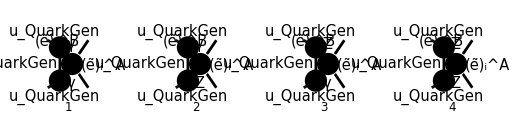

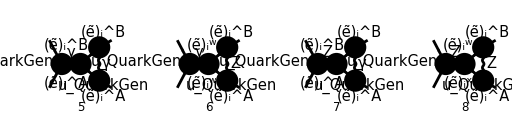

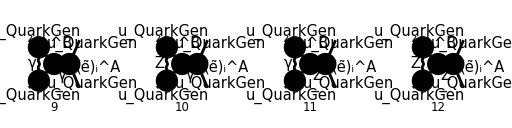

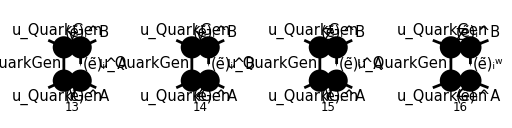

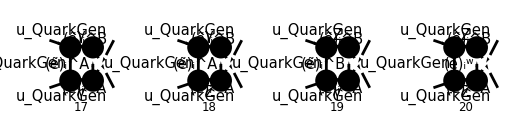

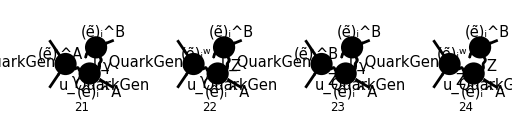

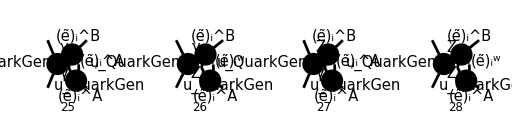

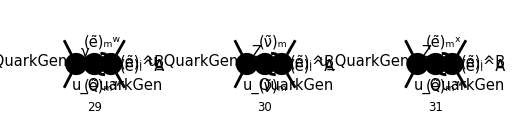

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{SelfEnergies,Tadpoles}],
{F[3,{QuarkGen}],-F[3,{QuarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],
S[13|14],
F[11|12],
V[3]
}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

## 05.04

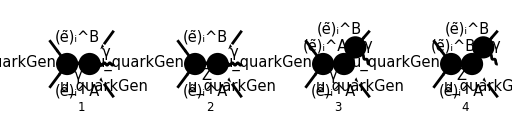

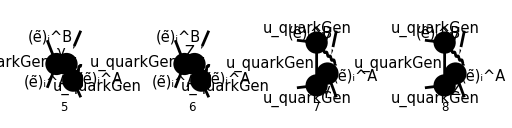

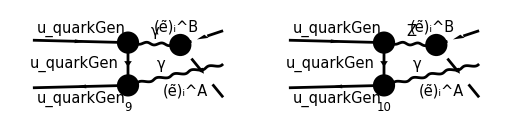

```mathematica
diags[0]=InsertFields[
CreateTopologies[0,2->3],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6]
}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k,k2},
LorentzIndexNames->{μ,ν,ρ,σ},
DropSumOver->True,
UndoChiralSplittings->True,
List->True,
SMP->True,
ChangeDimension->D
]/.{MQU[quarkGen]->0}
```

{-(2 ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) g^μρ (ε^*)^μ(k) g^νρ e^2)/(k+k_1+k_2)^2,(ⅈ (φ(-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) g^μρ (ε^*)^μ(k) g^νρ e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(((k+k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) (-k-2 k_1)^μ (ε^*)^μ(k) g^νρ (k+k_1-k_2)^ρ e^2)/((k+k_1+k_2)^2 ((-k-k_1)^2-m_l_iA^2)),(ⅈ (φ(-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-k-2 k_1)^μ (ε^*)^μ(k) g^νρ (k+k_1-k_2)^ρ e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 ((-k-k_1)^2-m_l_iB^2) ((k+k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) (-k-2 k_2)^μ (ε^*)^μ(k) g^νρ (k-k_1+k_2)^ρ e^2)/((k+k_1+k_2)^2 ((k+k_2)^2-m_l_iA^2)),(ⅈ (φ(-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-k-2 k_2)^μ (ε^*)^μ(k) g^νρ (k-k_1+k_2)^ρ e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 ((k+k_2)^2-m_l_iA^2) ((k+k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),((φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(γ·(k_1+k_2-p_2)).(-2/3 ⅈ γ^μ e).(φ(p_1)) IndexDelta(A,B) (ε^*)^μ(k) g^νρ (k_2-k_1)^ρ e)/((k_1+k_2)^2 (-k_1-k_2+p_2)^2),-(((φ(-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(γ·(k_1+k_2-p_2)).(-2/3 ⅈ γ^μ e).(φ(p_1)) (ε^*)^μ(k) g^νρ (k_2-k_1)^ρ e (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 (-k_1-k_2+p_2)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),((φ(-p_2)).(-2/3 ⅈ γ^μ e δ_Col1Col2).(γ·(k-p_2)).(-2/3 ⅈ γ^ν e).(φ(p_1)) IndexDelta(A,B) (ε^*)^μ(k) g^νρ (k_2-k_1)^ρ e)/((k_1+k_2)^2 (p_2-k)^2),-(((φ(-p_2)).(-2/3 ⅈ γ^μ e δ_Col1Col2).(γ·(k-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)))/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3))/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (ε^*)^μ(k) g^νρ (k_2-k_1)^ρ e (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 (p_2-k)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))))}

### Quark amplitude

```mathematica
Mrqγ[0]=(Mlist[0][[{7,9}]]//Total)(3/2SMP["e_Q"])^2
```

9/4 e_Q^2 ((e (k_2-k_1)^ρ g^νρ (ε^*)^μ(k) IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(γ·(k-p_2)).(-2/3 ⅈ e γ^ν).(φ(p_1)))/((k_1+k_2)^2 (p_2-k)^2)+(e (k_2-k_1)^ρ g^νρ (ε^*)^μ(k) IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^ν δ_Col1Col2).(γ·(k_1+k_2-p_2)).(-2/3 ⅈ e γ^μ).(φ(p_1)))/((k_1+k_2)^2 (-k_1-k_2+p_2)^2))

```mathematica
MrqZ[0]=(Mlist[0][[{8,10}]]//Total//ZSimplify)3/2SMP["e_Q"]
```

(3 e e_Q (k_2-k_1)^ρ g^νρ (ε^*)^μ(k) Z_l_i^AB (((φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(γ·(k-p_2)).(2 ⅈ e (γ^ν.(γ̄)^7 Z_q_L+γ^ν.(γ̄)^6 Z_q_R))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(p_2-k)^2+((φ(-p_2)).(2 ⅈ e δ_Col1Col2 (γ^ν.(γ̄)^7 Z_q_L+γ^ν.(γ̄)^6 Z_q_R))/((cos(θ_W)) (sin(θ_W))).(γ·(k_1+k_2-p_2)).(-2/3 ⅈ e γ^μ).(φ(p_1)))/(-k_1-k_2+p_2)^2))/(2 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2))

```mathematica
S[μ_,ρ_]:=GAD[μ].GSD[p1-k].GAD[ρ] FAD[p1-k]-GAD[ρ].GSD[p2-k].GAD[μ]FAD[p2-k];
```

```mathematica
MrqγHand[0]=SMP["e"]^3SMP["e_Q"]^2IndexDelta[A,B]FAD[k1+k2]SpinorVBarD[p2,0].S[μ,ρ].SpinorUD[p1,0] FVD[k1-k2,μ]ChangeDimension[Conjugate[PolarizationVector[k,ρ]],D]
```

(e^3 e_Q^2 (k_1-k_2)^μ (ε^*)^ρ(k) IndexDelta(A,B) v̄(p_2).((γ^μ.(γ·(p_1-k)).γ^ρ)/(p_1-k)^2-(γ^ρ.(γ·(p_2-k)).γ^μ)/(p_2-k)^2).u(p_1))/(k_1+k_2)^2

```mathematica
Γ5=Zql(1-GAD[5])+Zqr(1+GAD[5])
```

(1-(γ̄)^5) Z_q_L+((γ̄)^5+1) Z_q_R

```mathematica
MrqZHand[0]=-SMP["e"]^3SMP["e_Q"]ZliAB/(SMP["sin_W"]^2SMP["cos_W"]^2)FAD[{k1+k2,μZ}]SpinorVBarD[p2,0].S[μ,ρ].Γ5.SpinorUD[p1,0]FVD[k1-k2,μ]ChangeDimension[Conjugate[PolarizationVector[k,ρ]],D]
```

-(e^3 e_Q (k_1-k_2)^μ (ε^*)^ρ(k) Z_l_i^AB v̄(p_2).((γ^μ.(γ·(p_1-k)).γ^ρ)/(p_1-k)^2-(γ^ρ.(γ·(p_2-k)).γ^μ)/(p_2-k)^2).((1-(γ̄)^5) Z_q_L+((γ̄)^5+1) Z_q_R).u(p_1))/((cos(θ_W))^2 (sin(θ_W))^2 ((k_1+k_2)^2-μ_Z^2))

```mathematica
Mrq[0]=Mrqγ[0]+MrqZ[0]/.{SMP["m_Z"]->μZ}//FCE//ReplaceAll[#,{
FAD[-k1-k2+p2]->FAD[k-p1]
}]&//Contract
```

(3 e e_Q Z_l_i^AB ((4 e^2 δ_Col1Col2 (φ(-p_2)).(Z_q_L (γ·(k_2-k_1)).(γ̄)^7+Z_q_R (γ·(k_2-k_1)).(γ̄)^6).(γ·(k_1+k_2-p_2)).(γ·ε^*(k)).(φ(p_1)))/(3 (cos(θ_W)) (sin(θ_W)) (k-p_1)^2)+(4 e^2 δ_Col1Col2 (φ(-p_2)).(γ·ε^*(k)).(γ·(k-p_2)).(Z_q_L (γ·(k_2-k_1)).(γ̄)^7+Z_q_R (γ·(k_2-k_1)).(γ̄)^6).(φ(p_1)))/(3 (cos(θ_W)) (sin(θ_W)) (p_2-k)^2)))/(2 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-μ_Z^2))+9/4 e_Q^2 (-(4 e^3 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_2-k_1)).(γ·(k_1+k_2-p_2)).(γ·ε^*(k)).(φ(p_1)))/(9 (k_1+k_2)^2 (k-p_1)^2)-(4 e^3 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·ε^*(k)).(γ·(k-p_2)).(γ·(k_2-k_1)).(φ(p_1)))/(9 (k_1+k_2)^2 (p_2-k)^2))

```mathematica
MrqHand[0]=MrqγHand[0]+MrqZHand[0]//DiracSimplify//FullSimplify
FCCompareResults[{Mrq[0]},{MrqHand[0]}]
```

e^3 e_Q ((2 Z_l_i^AB ((Z_q_R (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))/(p_1-k)^2+(Z_q_L (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)))/(p_1-k)^2-(Z_q_R (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))/(p_1-k)^2-(Z_q_L (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)))/(p_1-k)^2-(2 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (p_1·ε^*(k)))/(p_1-k)^2-(2 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (p_1·ε^*(k)))/(p_1-k)^2+(2 Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (p_1·ε^*(k)))/(p_1-k)^2+(2 Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (p_1·ε^*(k)))/(p_1-k)^2-(Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)))/(p_2-k)^2-(Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1)))/(p_2-k)^2+(Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^6.(φ(p_1)))/(p_2-k)^2+(Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^7.(φ(p_1)))/(p_2-k)^2+1/(p_2-k)^2 2 (Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))-Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1))-Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))) (p_2·ε^*(k))))/(((k_1+k_2)^2-μ_Z^2) (cos(θ_W))^2 (sin(θ_W))^2)+1/(k_1+k_2)^2 IndexDelta(A,B) (-((φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(φ(p_1)))/(p_1-k)^2+((φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(φ(p_1)))/(p_1-k)^2+((φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(φ(p_1)))/(p_2-k)^2+2 ((φ(-p_2)).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(φ(p_1))) ((p_1·ε^*(k))/(p_1-k)^2-(p_2·ε^*(k))/(p_2-k)^2)) e_Q)

Check of the results: The results disagree.

False

```mathematica
Mrq[1]=Mrq[0]//FeynAmpDenominatorExplicit//FullSimplify
```

-((e^3 e_Q (IndexDelta(A,B) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (((φ(-p_2)).(γ·k_1).(γ·k_2).(γ·ε^*(k)).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·k_1).(γ·ε^*(k)).(φ(p_1))+(φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) (k_1^2-2 (k_1·p_2)-k_2^2+2 (k_2·p_2))) (k^2-2 (k·p_2)+p_2^2)+(k^2-2 (k·p_1)+p_1^2) ((φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(φ(p_1))+2 ((φ(-p_2)).(γ·k_2).(φ(p_1))-(φ(-p_2)).(γ·k_1).(φ(p_1))) (p_2·ε^*(k)))) (cos(θ_W))^2 e_Q (sin(θ_W))^2+2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2)+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2)-2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2)-2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2)+2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_1).(γ·k_2).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_1).(γ·k_2).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)-2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_2).(γ·k_1).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)-2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_2).(γ·k_1).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)+2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) k_1^2 (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) k_1^2 (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)-4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k_1·p_2) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)-4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k_1·p_2) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)-2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) k_2^2 (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)-2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) k_2^2 (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)+4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k_2·p_2) (k^2-2 (k·p_2)+p_2^2)+4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k_2·p_2) (k^2-2 (k·p_2)+p_2^2)-4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2) (p_2·ε^*(k))-4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2) (p_2·ε^*(k))+4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2) (p_2·ε^*(k))+4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2) (p_2·ε^*(k))) δ_Col1Col2)/((k_1^2+2 (k_1·k_2)+k_2^2) (-μ_Z^2+k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2) (k^2-2 (k·p_2)+p_2^2) (cos(θ_W))^2 (sin(θ_W))^2))

```mathematica
MrqHand[1]=MrqHand[0]//FeynAmpDenominatorExplicit//FullSimplify
```

e^3 e_Q ((2 Z_l_i^AB ((Z_q_R (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))/(k^2-2 (k·p_1)+p_1^2)-(2 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (p_1·ε^*(k)))/(k^2-2 (k·p_1)+p_1^2)-(2 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (p_1·ε^*(k)))/(k^2-2 (k·p_1)+p_1^2)+(2 Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (p_1·ε^*(k)))/(k^2-2 (k·p_1)+p_1^2)+(2 Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (p_1·ε^*(k)))/(k^2-2 (k·p_1)+p_1^2)+1/(k^2-2 (k·p_2)+p_2^2)2 (Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))-Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1))-Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))) (p_2·ε^*(k))+(Z_q_L (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)))/(k^2-2 (k·p_1)+p_1^2)-(Z_q_R (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))/(k^2-2 (k·p_1)+p_1^2)-(Z_q_L (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)))/(k^2-2 (k·p_1)+p_1^2)-(Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)))/(k^2-2 (k·p_2)+p_2^2)-(Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1)))/(k^2-2 (k·p_2)+p_2^2)+(Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^6.(φ(p_1)))/(k^2-2 (k·p_2)+p_2^2)+(Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^7.(φ(p_1)))/(k^2-2 (k·p_2)+p_2^2)))/((-μ_Z^2+k_1^2+2 (k_1·k_2)+k_2^2) (cos(θ_W))^2 (sin(θ_W))^2)+1/(k_1^2+2 (k_1·k_2)+k_2^2)IndexDelta(A,B) (((φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(φ(p_1)))/(k^2-2 (k·p_2)+p_2^2)+1/(k^2-2 (k·p_1)+p_1^2)(-(φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(φ(p_1))+(φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(φ(p_1))+2 ((φ(-p_2)).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(φ(p_1))) (p_1·ε^*(k)))+(2 ((φ(-p_2)).(γ·k_2).(φ(p_1))-(φ(-p_2)).(γ·k_1).(φ(p_1))) (p_2·ε^*(k)))/(k^2-2 (k·p_2)+p_2^2)) e_Q)

```mathematica
FCCompareResults[{Mrq[1]},{MrqHand[1]}]
```

Check of the results: The results disagree.

False

```mathematica
SPD[k]=0;
SPD[p1]=0;
SPD[p2]=0;
```

```mathematica
Mrq[1]//DiracSimplify//Simplify
MrqHand[1]
```

-((e^3 e_Q (-(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (k·p_1) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (cos(θ_W))^2 e_Q (sin(θ_W))^2+(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (k·p_1) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (cos(θ_W))^2 e_Q (sin(θ_W))^2-(φ(-p_2)).(γ·k_1).(γ·k_2).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) (k·p_2) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (cos(θ_W))^2 e_Q (sin(θ_W))^2+(φ(-p_2)).(γ·k_2).(γ·k_1).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) (k·p_2) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (cos(θ_W))^2 e_Q (sin(θ_W))^2+2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) (k·p_2) (k_1·p_2) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (cos(θ_W))^2 e_Q (sin(θ_W))^2+(φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) (k·p_2) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) k_2^2 (cos(θ_W))^2 e_Q (sin(θ_W))^2+(φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) (k·p_2) k_1^2 (-μ_Z^2+k_1^2+2 (k_1·k_2)+k_2^2) (cos(θ_W))^2 e_Q (sin(θ_W))^2-2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) (k·p_2) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (k_2·p_2) (cos(θ_W))^2 e_Q (sin(θ_W))^2+2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (k·p_1) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (p_2·ε^*(k)) (cos(θ_W))^2 e_Q (sin(θ_W))^2-2 (φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (k·p_1) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (p_2·ε^*(k)) (cos(θ_W))^2 e_Q (sin(θ_W))^2-2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2)-2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2)+2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^6.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2)+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^7.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2)-2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_1).(γ·k_2).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2)-2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_1).(γ·k_2).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2)+2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_2).(γ·k_1).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2)+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_2).(γ·k_1).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2)-2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·p_2) k_1^2 (k_1^2+2 (k_1·k_2)+k_2^2)-2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·p_2) k_1^2 (k_1^2+2 (k_1·k_2)+k_2^2)+4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·p_2) (k_1·p_2) (k_1^2+2 (k_1·k_2)+k_2^2)+4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·p_2) (k_1·p_2) (k_1^2+2 (k_1·k_2)+k_2^2)+2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·p_2) k_2^2 (k_1^2+2 (k_1·k_2)+k_2^2)+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·p_2) k_2^2 (k_1^2+2 (k_1·k_2)+k_2^2)-4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2) (k_2·p_2)-4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2) (k_2·p_2)+4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2) (p_2·ε^*(k))+4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2) (p_2·ε^*(k))-4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2) (p_2·ε^*(k))-4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2) (p_2·ε^*(k))) δ_Col1Col2)/(2 (k·p_1) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2) (-μ_Z^2+k_1^2+2 (k_1·k_2)+k_2^2) (cos(θ_W))^2 (sin(θ_W))^2))

e^3 e_Q ((2 Z_l_i^AB (-(Z_q_R (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))/(2 (k·p_1))+(Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (p_1·ε^*(k)))/(k·p_1)+(Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (p_1·ε^*(k)))/(k·p_1)-(Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (p_1·ε^*(k)))/(k·p_1)-(Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (p_1·ε^*(k)))/(k·p_1)-1/(k·p_2)(Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))-Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1))-Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))) (p_2·ε^*(k))-(Z_q_L (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)))/(2 (k·p_1))+(Z_q_R (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))/(2 (k·p_1))+(Z_q_L (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)))/(2 (k·p_1))+(Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)))/(2 (k·p_2))+(Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1)))/(2 (k·p_2))-(Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^6.(φ(p_1)))/(2 (k·p_2))-(Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^7.(φ(p_1)))/(2 (k·p_2))))/((-μ_Z^2+k_1^2+2 (k_1·k_2)+k_2^2) (cos(θ_W))^2 (sin(θ_W))^2)+1/(k_1^2+2 (k_1·k_2)+k_2^2)IndexDelta(A,B) (-((φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(φ(p_1)))/(2 (k·p_2))-1/(2 (k·p_1))(-(φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(φ(p_1))+(φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(φ(p_1))+2 ((φ(-p_2)).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(φ(p_1))) (p_1·ε^*(k)))-(((φ(-p_2)).(γ·k_2).(φ(p_1))-(φ(-p_2)).(γ·k_1).(φ(p_1))) (p_2·ε^*(k)))/(k·p_2)) e_Q)

## 06.04

```mathematica
FCClearScalarProducts[];
SPD[p1]=0;
SPD[p2]=0;
SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(Q^2-m1^2-m2^2)/2;
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[x,{p1,p2,-k1,-k2,-k},{0,0,m1,m2,0}];
```

```mathematica
FCClearScalarProducts[];
SPD[p1]=0;
SPD[p2]=0;
SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(Q^2-m1^2-m2^2)/2;
SPD[p1,k]=xp1;
SPD[p2,k]=xp2;
SPD[k1,k]=x1;
SPD[k2,k]=x2;
SPD[p1,k1]=u;
MakeBoxes[xp1,TraditionalForm]:=SubscriptBox["x","p1"];
MakeBoxes[xp2,TraditionalForm]:=SubscriptBox["x","p2"];
```

```mathematica
DiracTrace[GSD[p2].GSD[k1-k2].GSD[k-p1].GSD[k+2k1].GSD[p1].GSD[k2]]
%//DiracSimplify//FullSimplify
%/.{
SPD[p1,k2]->SPD[p1,p2]-SPD[p1,k]-SPD[p1,k1],
SPD[p2,k1]->m1^2+SPD[k1,k2]+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->(m1^2-m2^2)/2+SPD[k1,k]-SPD[p1,k]-SPD[p1,k1]
}//FullSimplify
```

tr((γ·p_2).(γ·(k_1-k_2)).(γ·(k-p_1)).(γ·(k+2 k_1)).(γ·p_1).(γ·k_2))

-2 (-m_1^2 (2 (x_p1 (m_2^2+2 (x_p1+x_p2-x_1)+Q^2)+u (-3 x_p1+2 x_p2+4 x_1-2 x_2)-6 u^2)+s (x_p1-2 x_p2+2 u+2 x_2))+m_2^2 (-2 (u (5 x_p1+2 x_p2+2 x_2)+2 x_p1 (x_p1-x_1)+2 u^2)+6 Q^2 x_p1+s (3 x_p1+6 u-2 x_1))+4 m_1^4 x_p1-6 m_2^4 x_p1+x_p1 (Q^2 (s-8 u+4 x_1)+2 s (5 u-3 x_1)-8 u (5 u-4 x_1+x_2))+4 x_p1^2 (s-8 u+3 x_1)-8 x_p1^3+2 (u-x_1) (Q^2 (s-4 u)+2 u (s-4 u+2 x_1-2 x_2)))

-2 (-m_1^2 (2 (x_p1 (m_2^2+2 (x_p1+x_p2-x_1)+Q^2)+u (-3 x_p1+2 x_p2+4 x_1-2 x_2)-6 u^2)+s (x_p1-2 x_p2+2 u+2 x_2))+m_2^2 (-2 (u (5 x_p1+2 x_p2+2 x_2)+2 x_p1 (x_p1-x_1)+2 u^2)+6 Q^2 x_p1+s (3 x_p1+6 u-2 x_1))+4 m_1^4 x_p1-6 m_2^4 x_p1+x_p1 (Q^2 (s-8 u+4 x_1)+2 s (5 u-3 x_1)-8 u (5 u-4 x_1+x_2))+4 x_p1^2 (s-8 u+3 x_1)-8 x_p1^3+2 (u-x_1) (Q^2 (s-4 u)+2 u (s-4 u+2 x_1-2 x_2)))

```mathematica
%/.{xp1->0,xp2->0,x1->0,x2->0}//FullSimplify
```

4 u (m_1^2 (s-6 u)+m_2^2 (2 u-3 s)-(Q^2+2 u) (s-4 u))

## 07.04

```mathematica
(4 Pi)^((d-3)/2)Gamma[(d-1)/2]
%//ReplaceAll[#,{d->4}]&
```

2^(d-3) π^((d-3)/2) (d-1)/2

π

```mathematica
Gamma[3/2]
```

(√π)/2

```mathematica
Hold[ 3Pi p^(d-4)/((d-1)(4Pi)^((d-3)/2)Gamma[(d-1)/2])]
%/.{d->4}//FRH
```

Hold[(3 π p^(d-4))/((d-1) (4 π)^((d-3)/2) (d-1)/2)]

1